```mathematica
CartesianProduct[listM_,listN_]:=
Module[
{list :={},
listOmega:=listM,
listOmega2:= listN
},
{
generateListsOfPairs[current_]:=
Module[
{
currentAlpha=current,
iterator=1,
iteratorb=1

},
{
(*Print[sizeOfN];*)

While[
iterator<Length[listOmega]+1, 
(*Reset inner iterator*)
iteratorb=1;
While[
iteratorb<Length[listOmega2]+1,
AppendTo[list,{listOmega[[iterator]],listOmega2[[iteratorb]]}];
iteratorb++
];
iterator++
];
}
];

generateListsOfPairs[{}];
list
}
]
```

```mathematica
foo=CartesianProduct[Table[i,{i,1,50}],Table[i,{i,1,50}]]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},2440,{50,21},{50,22},{50,23},{50,24},{50,25},{50,26},{50,27},{50,28},{50,29},{50,30},{50,31},{50,32},{50,33},{50,34},{50,35},{50,36},{50,37},{50,38},{50,39},{50,40},{50,41},{50,42},{50,43},{50,44},{50,45},{50,46},{50,47},{50,48},{50,49},{50,50}}}
 |  |  |  |

```mathematica
foo[[1,1,2]]
foo[[1,2]]
```

1

{1,2}

```mathematica
congruenceModN[theList_,n_]:=Module[
{
list={},
iterator=1
},
{
While[
iterator <Length[theList[[1]]],
{
If[
And[
Mod[Abs[theList[[1,iterator,1]]-theList[[1,iterator,2]]],n]==0,
theList[[1,iterator,1]]-theList[[1,iterator,2]]>0
],
{AppendTo[list,theList[[1,iterator]]]
},
{}
];
iterator++
}
];
list

}
]
```

```mathematica
Function[theList,Module[{list:={},iterator:=1},{While[iterator<Length[theList],{If[Mod[Abs[theList⟦1,iterator,1⟧-theList⟦1,iterator,2⟧],3]==0,{AppendTo[list,theList⟦1,i⟧]},Print["foo"]];iterator++}];list}]]
```

Function[theList,Module[{list:={},iterator:=1},{While[iterator<Length[theList],{If[Mod[Abs[theList⟦1,iterator,1⟧-theList⟦1,iterator,2⟧],3]==0,{AppendTo[list,theList⟦1,i⟧]},Print[foo]];iterator++}];list}]]

```mathematica
result=congruenceModN[foo]
```

{{{1,1},{1,4},{1,7},{1,10},{1,13},{1,16},{1,19},{1,22},{1,25},{1,28},{1,31},{1,34},{1,37},{1,40},{1,43},{1,46},{1,49},{2,2},{2,5},{2,8},{2,11},{2,14},{2,17},{2,20},{2,23},{2,26},{2,29},{2,32},{2,35},{2,38},{2,41},{2,44},{2,47},{2,50},{3,3},{3,6},{3,9},{3,12},{3,15},{3,18},{3,21},{3,24},{3,27},{3,30},{3,33},{3,36},{3,39},{3,42},{3,45},{3,48},{4,1},{4,4},{4,7},{4,10},{4,13},{4,16},{4,19},{4,22},{4,25},{4,28},{4,31},{4,34},{4,37},{4,40},{4,43},{4,46},{4,49},{5,2},{5,5},{5,8},{5,11},{5,14},{5,17},{5,20},{5,23},{5,26},{5,29},{5,32},{5,35},{5,38},{5,41},{5,44},{5,47},{5,50},{6,3},{6,6},{6,9},{6,12},{6,15},{6,18},{6,21},{6,24},{6,27},{6,30},{6,33},{6,36},{6,39},{6,42},{6,45},{6,48},{7,1},{7,4},{7,7},{7,10},{7,13},{7,16},{7,19},{7,22},{7,25},{7,28},{7,31},{7,34},{7,37},{7,40},{7,43},{7,46},{7,49},{8,2},{8,5},{8,8},{8,11},{8,14},{8,17},{8,20},{8,23},{8,26},{8,29},{8,32},{8,35},{8,38},{8,41},{8,44},{8,47},{8,50},{9,3},{9,6},{9,9},{9,12},{9,15},{9,18},{9,21},{9,24},{9,27},{9,30},{9,33},{9,36},{9,39},{9,42},{9,45},{9,48},{10,1},{10,4},{10,7},{10,10},{10,13},{10,16},{10,19},{10,22},{10,25},{10,28},{10,31},{10,34},{10,37},{10,40},{10,43},{10,46},{10,49},{11,2},{11,5},{11,8},{11,11},{11,14},{11,17},{11,20},{11,23},{11,26},{11,29},{11,32},{11,35},{11,38},{11,41},{11,44},{11,47},{11,50},{12,3},{12,6},{12,9},{12,12},{12,15},{12,18},{12,21},{12,24},{12,27},{12,30},{12,33},{12,36},{12,39},{12,42},{12,45},{12,48},{13,1},{13,4},{13,7},{13,10},{13,13},{13,16},{13,19},{13,22},{13,25},{13,28},{13,31},{13,34},{13,37},{13,40},{13,43},{13,46},{13,49},{14,2},{14,5},{14,8},{14,11},{14,14},{14,17},{14,20},{14,23},{14,26},{14,29},{14,32},{14,35},{14,38},{14,41},{14,44},{14,47},{14,50},{15,3},{15,6},{15,9},{15,12},{15,15},{15,18},{15,21},{15,24},{15,27},{15,30},{15,33},{15,36},{15,39},{15,42},{15,45},{15,48},{16,1},{16,4},{16,7},{16,10},{16,13},{16,16},{16,19},{16,22},{16,25},{16,28},{16,31},{16,34},{16,37},{16,40},{16,43},{16,46},{16,49},{17,2},{17,5},{17,8},{17,11},{17,14},{17,17},{17,20},{17,23},{17,26},{17,29},{17,32},{17,35},{17,38},{17,41},{17,44},{17,47},{17,50},{18,3},{18,6},{18,9},{18,12},{18,15},{18,18},{18,21},{18,24},{18,27},{18,30},{18,33},{18,36},{18,39},{18,42},{18,45},{18,48},{19,1},{19,4},{19,7},{19,10},{19,13},{19,16},{19,19},{19,22},{19,25},{19,28},{19,31},{19,34},{19,37},{19,40},{19,43},{19,46},{19,49},{20,2},{20,5},{20,8},{20,11},{20,14},{20,17},{20,20},{20,23},{20,26},{20,29},{20,32},{20,35},{20,38},{20,41},{20,44},{20,47},{20,50},{21,3},{21,6},{21,9},{21,12},{21,15},{21,18},{21,21},{21,24},{21,27},{21,30},{21,33},{21,36},{21,39},{21,42},{21,45},{21,48},{22,1},{22,4},{22,7},{22,10},{22,13},{22,16},{22,19},{22,22},{22,25},{22,28},{22,31},{22,34},{22,37},{22,40},{22,43},{22,46},{22,49},{23,2},{23,5},{23,8},{23,11},{23,14},{23,17},{23,20},{23,23},{23,26},{23,29},{23,32},{23,35},{23,38},{23,41},{23,44},{23,47},{23,50},{24,3},{24,6},{24,9},{24,12},{24,15},{24,18},{24,21},{24,24},{24,27},{24,30},{24,33},{24,36},{24,39},{24,42},{24,45},{24,48},{25,1},{25,4},{25,7},{25,10},{25,13},{25,16},{25,19},{25,22},{25,25},{25,28},{25,31},{25,34},{25,37},{25,40},{25,43},{25,46},{25,49},{26,2},{26,5},{26,8},{26,11},{26,14},{26,17},{26,20},{26,23},{26,26},{26,29},{26,32},{26,35},{26,38},{26,41},{26,44},{26,47},{26,50},{27,3},{27,6},{27,9},{27,12},{27,15},{27,18},{27,21},{27,24},{27,27},{27,30},{27,33},{27,36},{27,39},{27,42},{27,45},{27,48},{28,1},{28,4},{28,7},{28,10},{28,13},{28,16},{28,19},{28,22},{28,25},{28,28},{28,31},{28,34},{28,37},{28,40},{28,43},{28,46},{28,49},{29,2},{29,5},{29,8},{29,11},{29,14},{29,17},{29,20},{29,23},{29,26},{29,29},{29,32},{29,35},{29,38},{29,41},{29,44},{29,47},{29,50},{30,3},{30,6},{30,9},{30,12},{30,15},{30,18},{30,21},{30,24},{30,27},{30,30},{30,33},{30,36},{30,39},{30,42},{30,45},{30,48},{31,1},{31,4},{31,7},{31,10},{31,13},{31,16},{31,19},{31,22},{31,25},{31,28},{31,31},{31,34},{31,37},{31,40},{31,43},{31,46},{31,49},{32,2},{32,5},{32,8},{32,11},{32,14},{32,17},{32,20},{32,23},{32,26},{32,29},{32,32},{32,35},{32,38},{32,41},{32,44},{32,47},{32,50},{33,3},{33,6},{33,9},{33,12},{33,15},{33,18},{33,21},{33,24},{33,27},{33,30},{33,33},{33,36},{33,39},{33,42},{33,45},{33,48},{34,1},{34,4},{34,7},{34,10},{34,13},{34,16},{34,19},{34,22},{34,25},{34,28},{34,31},{34,34},{34,37},{34,40},{34,43},{34,46},{34,49},{35,2},{35,5},{35,8},{35,11},{35,14},{35,17},{35,20},{35,23},{35,26},{35,29},{35,32},{35,35},{35,38},{35,41},{35,44},{35,47},{35,50},{36,3},{36,6},{36,9},{36,12},{36,15},{36,18},{36,21},{36,24},{36,27},{36,30},{36,33},{36,36},{36,39},{36,42},{36,45},{36,48},{37,1},{37,4},{37,7},{37,10},{37,13},{37,16},{37,19},{37,22},{37,25},{37,28},{37,31},{37,34},{37,37},{37,40},{37,43},{37,46},{37,49},{38,2},{38,5},{38,8},{38,11},{38,14},{38,17},{38,20},{38,23},{38,26},{38,29},{38,32},{38,35},{38,38},{38,41},{38,44},{38,47},{38,50},{39,3},{39,6},{39,9},{39,12},{39,15},{39,18},{39,21},{39,24},{39,27},{39,30},{39,33},{39,36},{39,39},{39,42},{39,45},{39,48},{40,1},{40,4},{40,7},{40,10},{40,13},{40,16},{40,19},{40,22},{40,25},{40,28},{40,31},{40,34},{40,37},{40,40},{40,43},{40,46},{40,49},{41,2},{41,5},{41,8},{41,11},{41,14},{41,17},{41,20},{41,23},{41,26},{41,29},{41,32},{41,35},{41,38},{41,41},{41,44},{41,47},{41,50},{42,3},{42,6},{42,9},{42,12},{42,15},{42,18},{42,21},{42,24},{42,27},{42,30},{42,33},{42,36},{42,39},{42,42},{42,45},{42,48},{43,1},{43,4},{43,7},{43,10},{43,13},{43,16},{43,19},{43,22},{43,25},{43,28},{43,31},{43,34},{43,37},{43,40},{43,43},{43,46},{43,49},{44,2},{44,5},{44,8},{44,11},{44,14},{44,17},{44,20},{44,23},{44,26},{44,29},{44,32},{44,35},{44,38},{44,41},{44,44},{44,47},{44,50},{45,3},{45,6},{45,9},{45,12},{45,15},{45,18},{45,21},{45,24},{45,27},{45,30},{45,33},{45,36},{45,39},{45,42},{45,45},{45,48},{46,1},{46,4},{46,7},{46,10},{46,13},{46,16},{46,19},{46,22},{46,25},{46,28},{46,31},{46,34},{46,37},{46,40},{46,43},{46,46},{46,49},{47,2},{47,5},{47,8},{47,11},{47,14},{47,17},{47,20},{47,23},{47,26},{47,29},{47,32},{47,35},{47,38},{47,41},{47,44},{47,47},{47,50},{48,3},{48,6},{48,9},{48,12},{48,15},{48,18},{48,21},{48,24},{48,27},{48,30},{48,33},{48,36},{48,39},{48,42},{48,45},{48,48},{49,1},{49,4},{49,7},{49,10},{49,13},{49,16},{49,19},{49,22},{49,25},{49,28},{49,31},{49,34},{49,37},{49,40},{49,43},{49,46},{49,49},{50,2},{50,5},{50,8},{50,11},{50,14},{50,17},{50,20},{50,23},{50,26},{50,29},{50,32},{50,35},{50,38},{50,41},{50,44},{50,47}}}

```mathematica
Length@result[[1]]
```

833

```mathematica
Length@foo[[1]]
```

2500

```mathematica
result2 = congruenceModN[foo,3]
```

```mathematica
foo25=CartesianProduct[Table[i,{i,1,25}],Table[i,{i,1,25}]]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{2,21},{2,22},{2,23},{2,24},{2,25},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{3,21},{3,22},{3,23},{3,24},{3,25},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{4,21},{4,22},{4,23},{4,24},{4,25},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{5,21},{5,22},{5,23},{5,24},{5,25},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20},{6,21},{6,22},{6,23},{6,24},{6,25},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20},{7,21},{7,22},{7,23},{7,24},{7,25},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20},{8,21},{8,22},{8,23},{8,24},{8,25},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{9,25},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{10,25},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21},{11,22},{11,23},{11,24},{11,25},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,12},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{12,25},{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,13},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21},{13,22},{13,23},{13,24},{13,25},{14,1},{14,2},{14,3},{14,4},{14,5},{14,6},{14,7},{14,8},{14,9},{14,10},{14,11},{14,12},{14,13},{14,14},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21},{14,22},{14,23},{14,24},{14,25},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{15,7},{15,8},{15,9},{15,10},{15,11},{15,12},{15,13},{15,14},{15,15},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,23},{15,24},{15,25},{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,16},{16,17},{16,18},{16,19},{16,20},{16,21},{16,22},{16,23},{16,24},{16,25},{17,1},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{17,8},{17,9},{17,10},{17,11},{17,12},{17,13},{17,14},{17,15},{17,16},{17,17},{17,18},{17,19},{17,20},{17,21},{17,22},{17,23},{17,24},{17,25},{18,1},{18,2},{18,3},{18,4},{18,5},{18,6},{18,7},{18,8},{18,9},{18,10},{18,11},{18,12},{18,13},{18,14},{18,15},{18,16},{18,17},{18,18},{18,19},{18,20},{18,21},{18,22},{18,23},{18,24},{18,25},{19,1},{19,2},{19,3},{19,4},{19,5},{19,6},{19,7},{19,8},{19,9},{19,10},{19,11},{19,12},{19,13},{19,14},{19,15},{19,16},{19,17},{19,18},{19,19},{19,20},{19,21},{19,22},{19,23},{19,24},{19,25},{20,1},{20,2},{20,3},{20,4},{20,5},{20,6},{20,7},{20,8},{20,9},{20,10},{20,11},{20,12},{20,13},{20,14},{20,15},{20,16},{20,17},{20,18},{20,19},{20,20},{20,21},{20,22},{20,23},{20,24},{20,25},{21,1},{21,2},{21,3},{21,4},{21,5},{21,6},{21,7},{21,8},{21,9},{21,10},{21,11},{21,12},{21,13},{21,14},{21,15},{21,16},{21,17},{21,18},{21,19},{21,20},{21,21},{21,22},{21,23},{21,24},{21,25},{22,1},{22,2},{22,3},{22,4},{22,5},{22,6},{22,7},{22,8},{22,9},{22,10},{22,11},{22,12},{22,13},{22,14},{22,15},{22,16},{22,17},{22,18},{22,19},{22,20},{22,21},{22,22},{22,23},{22,24},{22,25},{23,1},{23,2},{23,3},{23,4},{23,5},{23,6},{23,7},{23,8},{23,9},{23,10},{23,11},{23,12},{23,13},{23,14},{23,15},{23,16},{23,17},{23,18},{23,19},{23,20},{23,21},{23,22},{23,23},{23,24},{23,25},{24,1},{24,2},{24,3},{24,4},{24,5},{24,6},{24,7},{24,8},{24,9},{24,10},{24,11},{24,12},{24,13},{24,14},{24,15},{24,16},{24,17},{24,18},{24,19},{24,20},{24,21},{24,22},{24,23},{24,24},{24,25},{25,1},{25,2},{25,3},{25,4},{25,5},{25,6},{25,7},{25,8},{25,9},{25,10},{25,11},{25,12},{25,13},{25,14},{25,15},{25,16},{25,17},{25,18},{25,19},{25,20},{25,21},{25,22},{25,23},{25,24},{25,25}}}

```mathematica
primes10=Table[Prime[i],{i,1,10}]
result25and10Primes = Table[congruenceModN[foo25,primes10[[i]]],{i,1,10}];
sizeOfSets=Table[Length[result25and10Primes[[i,1]]],{i,1,Length@result25and10Primes}]
Length@foo25[[1]]
```

{2,3,5,7,11,13,17,19,23,29}

{1,1,1,1,1,1,1,1,1,1}

625

```mathematica
congruenceAmodN[a_,theList_,n_]:=Module[
{
list={},
iterator=1
},

While[
iterator <Length[theList]+1,

If[
And[
Mod[Abs[a-theList[[iterator]]],n]==0
(*theList[[iterator,1]]-theList[[iterator,2]]>0*)
],
AppendTo[list,theList[[iterator]]]
,
{}
];
iterator++

];
list

]
```

```mathematica
numbers=Table[i,{i,1,25}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
congruenceAmodN[0,numbers,2]
congruenceAmodN[1,numbers,2]
```

```mathematica
congruenceAmodN[0,numbers,7]

congruenceAmodN[1,numbers,7]

congruenceAmodN[2,numbers,7]

congruenceAmodN[3,numbers,7]

congruenceAmodN[4,numbers,7]

congruenceAmodN[5,numbers,7]

congruenceAmodN[6,numbers,7]

congruenceAmodN[7,numbers,7]
```

{7,14,21}

{1,8,15,22}

{2,9,16,23}

{3,10,17,24}

{4,11,18,25}

{5,12,19}

{6,13,20}

{7,14,21}

```mathematica
congruenceAmodN[0,numbers,3]

congruenceAmodN[1,numbers,3]

congruenceAmodN[2,numbers,3]
```

{3,6,9,12,15,18,21,24}

{1,4,7,10,13,16,19,22,25}

{2,5,8,11,14,17,20,23}

```mathematica
congruenceModN[theList_,n_]:=Module[
{
list={},
iterator=1
},

While[
iterator <Length[theList],

If[
And[
Mod[Abs[theList[[iterator,1]]-theList[[iterator,2]]],n]==0
(*theList[[iterator,1]]-theList[[iterator,2]]>0*)
],
AppendTo[list,theList[[iterator]]]
,
{}
];
iterator++

];
list

]
```

```mathematica
trial1=congruenceModN[foo25[[1]],2]
foo25[[1]]
```

{{3,1},{4,2},{5,1},{5,3},{6,2},{6,4},{7,1},{7,3},{7,5},{8,2},{8,4},{8,6},{9,1},{9,3},{9,5},{9,7},{10,2},{10,4},{10,6},{10,8},{11,1},{11,3},{11,5},{11,7},{11,9},{12,2},{12,4},{12,6},{12,8},{12,10},{13,1},{13,3},{13,5},{13,7},{13,9},{13,11},{14,2},{14,4},{14,6},{14,8},{14,10},{14,12},{15,1},{15,3},{15,5},{15,7},{15,9},{15,11},{15,13},{16,2},{16,4},{16,6},{16,8},{16,10},{16,12},{16,14},{17,1},{17,3},{17,5},{17,7},{17,9},{17,11},{17,13},{17,15},{18,2},{18,4},{18,6},{18,8},{18,10},{18,12},{18,14},{18,16},{19,1},{19,3},{19,5},{19,7},{19,9},{19,11},{19,13},{19,15},{19,17},{20,2},{20,4},{20,6},{20,8},{20,10},{20,12},{20,14},{20,16},{20,18},{21,1},{21,3},{21,5},{21,7},{21,9},{21,11},{21,13},{21,15},{21,17},{21,19},{22,2},{22,4},{22,6},{22,8},{22,10},{22,12},{22,14},{22,16},{22,18},{22,20},{23,1},{23,3},{23,5},{23,7},{23,9},{23,11},{23,13},{23,15},{23,17},{23,19},{23,21},{24,2},{24,4},{24,6},{24,8},{24,10},{24,12},{24,14},{24,16},{24,18},{24,20},{24,22},{25,1},{25,3},{25,5},{25,7},{25,9},{25,11},{25,13},{25,15},{25,17},{25,19},{25,21},{25,23}}

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{2,21},{2,22},{2,23},{2,24},{2,25},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{3,21},{3,22},{3,23},{3,24},{3,25},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{4,21},{4,22},{4,23},{4,24},{4,25},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{5,21},{5,22},{5,23},{5,24},{5,25},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20},{6,21},{6,22},{6,23},{6,24},{6,25},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20},{7,21},{7,22},{7,23},{7,24},{7,25},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20},{8,21},{8,22},{8,23},{8,24},{8,25},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{9,25},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{10,25},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21},{11,22},{11,23},{11,24},{11,25},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,12},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{12,25},{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,13},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21},{13,22},{13,23},{13,24},{13,25},{14,1},{14,2},{14,3},{14,4},{14,5},{14,6},{14,7},{14,8},{14,9},{14,10},{14,11},{14,12},{14,13},{14,14},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21},{14,22},{14,23},{14,24},{14,25},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{15,7},{15,8},{15,9},{15,10},{15,11},{15,12},{15,13},{15,14},{15,15},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,23},{15,24},{15,25},{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,16},{16,17},{16,18},{16,19},{16,20},{16,21},{16,22},{16,23},{16,24},{16,25},{17,1},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{17,8},{17,9},{17,10},{17,11},{17,12},{17,13},{17,14},{17,15},{17,16},{17,17},{17,18},{17,19},{17,20},{17,21},{17,22},{17,23},{17,24},{17,25},{18,1},{18,2},{18,3},{18,4},{18,5},{18,6},{18,7},{18,8},{18,9},{18,10},{18,11},{18,12},{18,13},{18,14},{18,15},{18,16},{18,17},{18,18},{18,19},{18,20},{18,21},{18,22},{18,23},{18,24},{18,25},{19,1},{19,2},{19,3},{19,4},{19,5},{19,6},{19,7},{19,8},{19,9},{19,10},{19,11},{19,12},{19,13},{19,14},{19,15},{19,16},{19,17},{19,18},{19,19},{19,20},{19,21},{19,22},{19,23},{19,24},{19,25},{20,1},{20,2},{20,3},{20,4},{20,5},{20,6},{20,7},{20,8},{20,9},{20,10},{20,11},{20,12},{20,13},{20,14},{20,15},{20,16},{20,17},{20,18},{20,19},{20,20},{20,21},{20,22},{20,23},{20,24},{20,25},{21,1},{21,2},{21,3},{21,4},{21,5},{21,6},{21,7},{21,8},{21,9},{21,10},{21,11},{21,12},{21,13},{21,14},{21,15},{21,16},{21,17},{21,18},{21,19},{21,20},{21,21},{21,22},{21,23},{21,24},{21,25},{22,1},{22,2},{22,3},{22,4},{22,5},{22,6},{22,7},{22,8},{22,9},{22,10},{22,11},{22,12},{22,13},{22,14},{22,15},{22,16},{22,17},{22,18},{22,19},{22,20},{22,21},{22,22},{22,23},{22,24},{22,25},{23,1},{23,2},{23,3},{23,4},{23,5},{23,6},{23,7},{23,8},{23,9},{23,10},{23,11},{23,12},{23,13},{23,14},{23,15},{23,16},{23,17},{23,18},{23,19},{23,20},{23,21},{23,22},{23,23},{23,24},{23,25},{24,1},{24,2},{24,3},{24,4},{24,5},{24,6},{24,7},{24,8},{24,9},{24,10},{24,11},{24,12},{24,13},{24,14},{24,15},{24,16},{24,17},{24,18},{24,19},{24,20},{24,21},{24,22},{24,23},{24,24},{24,25},{25,1},{25,2},{25,3},{25,4},{25,5},{25,6},{25,7},{25,8},{25,9},{25,10},{25,11},{25,12},{25,13},{25,14},{25,15},{25,16},{25,17},{25,18},{25,19},{25,20},{25,21},{25,22},{25,23},{25,24},{25,25}}

```mathematica
result25and10PrimesFunc[listOfPairs_,nNumberOfPrimes_]:=
Module[
{resultList:={}
},


For[
i=1,
i<Length[nNumberOfPrimes],
i++,
AppendTo[resultList,congruenceModN[listOfPairs,nNumberOfPrimes[[i]]]]
];
resultList

]
```

```mathematica
foo25[[1]]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{2,21},{2,22},{2,23},{2,24},{2,25},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{3,21},{3,22},{3,23},{3,24},{3,25},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{4,21},{4,22},{4,23},{4,24},{4,25},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{5,21},{5,22},{5,23},{5,24},{5,25},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20},{6,21},{6,22},{6,23},{6,24},{6,25},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20},{7,21},{7,22},{7,23},{7,24},{7,25},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20},{8,21},{8,22},{8,23},{8,24},{8,25},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{9,25},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{10,25},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21},{11,22},{11,23},{11,24},{11,25},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,12},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{12,25},{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,13},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21},{13,22},{13,23},{13,24},{13,25},{14,1},{14,2},{14,3},{14,4},{14,5},{14,6},{14,7},{14,8},{14,9},{14,10},{14,11},{14,12},{14,13},{14,14},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21},{14,22},{14,23},{14,24},{14,25},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{15,7},{15,8},{15,9},{15,10},{15,11},{15,12},{15,13},{15,14},{15,15},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,23},{15,24},{15,25},{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,16},{16,17},{16,18},{16,19},{16,20},{16,21},{16,22},{16,23},{16,24},{16,25},{17,1},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{17,8},{17,9},{17,10},{17,11},{17,12},{17,13},{17,14},{17,15},{17,16},{17,17},{17,18},{17,19},{17,20},{17,21},{17,22},{17,23},{17,24},{17,25},{18,1},{18,2},{18,3},{18,4},{18,5},{18,6},{18,7},{18,8},{18,9},{18,10},{18,11},{18,12},{18,13},{18,14},{18,15},{18,16},{18,17},{18,18},{18,19},{18,20},{18,21},{18,22},{18,23},{18,24},{18,25},{19,1},{19,2},{19,3},{19,4},{19,5},{19,6},{19,7},{19,8},{19,9},{19,10},{19,11},{19,12},{19,13},{19,14},{19,15},{19,16},{19,17},{19,18},{19,19},{19,20},{19,21},{19,22},{19,23},{19,24},{19,25},{20,1},{20,2},{20,3},{20,4},{20,5},{20,6},{20,7},{20,8},{20,9},{20,10},{20,11},{20,12},{20,13},{20,14},{20,15},{20,16},{20,17},{20,18},{20,19},{20,20},{20,21},{20,22},{20,23},{20,24},{20,25},{21,1},{21,2},{21,3},{21,4},{21,5},{21,6},{21,7},{21,8},{21,9},{21,10},{21,11},{21,12},{21,13},{21,14},{21,15},{21,16},{21,17},{21,18},{21,19},{21,20},{21,21},{21,22},{21,23},{21,24},{21,25},{22,1},{22,2},{22,3},{22,4},{22,5},{22,6},{22,7},{22,8},{22,9},{22,10},{22,11},{22,12},{22,13},{22,14},{22,15},{22,16},{22,17},{22,18},{22,19},{22,20},{22,21},{22,22},{22,23},{22,24},{22,25},{23,1},{23,2},{23,3},{23,4},{23,5},{23,6},{23,7},{23,8},{23,9},{23,10},{23,11},{23,12},{23,13},{23,14},{23,15},{23,16},{23,17},{23,18},{23,19},{23,20},{23,21},{23,22},{23,23},{23,24},{23,25},{24,1},{24,2},{24,3},{24,4},{24,5},{24,6},{24,7},{24,8},{24,9},{24,10},{24,11},{24,12},{24,13},{24,14},{24,15},{24,16},{24,17},{24,18},{24,19},{24,20},{24,21},{24,22},{24,23},{24,24},{24,25},{25,1},{25,2},{25,3},{25,4},{25,5},{25,6},{25,7},{25,8},{25,9},{25,10},{25,11},{25,12},{25,13},{25,14},{25,15},{25,16},{25,17},{25,18},{25,19},{25,20},{25,21},{25,22},{25,23},{25,24},{25,25}}

```mathematica
foo25[[1,1]]
primes10;

(*result25and10PrimesFromFunc=result25and10PrimesFunc[foo25[[1]],primes10]*)
relaxedResult2510PrimesFromFunc=result25and10PrimesFunc[foo25[[1]],primes10]
```

{1,1}

{{{1,1},{1,3},{1,5},{1,7},{1,9},{1,11},{1,13},{1,15},{1,17},{1,19},{1,21},{1,23},{1,25},{2,2},{2,4},{2,6},{2,8},{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{2,24},{3,1},{3,3},{3,5},{3,7},{3,9},{3,11},{3,13},{3,15},{3,17},{3,19},{3,21},{3,23},{3,25},{4,2},{4,4},{4,6},{4,8},{4,10},{4,12},{4,14},{4,16},{4,18},{4,20},{4,22},{4,24},{5,1},{5,3},{5,5},{5,7},{5,9},{5,11},{5,13},{5,15},{5,17},{5,19},{5,21},{5,23},{5,25},{6,2},{6,4},{6,6},{6,8},{6,10},{6,12},{6,14},{6,16},{6,18},{6,20},{6,22},{6,24},{7,1},{7,3},{7,5},{7,7},{7,9},{7,11},{7,13},{7,15},{7,17},{7,19},{7,21},{7,23},{7,25},{8,2},{8,4},{8,6},{8,8},{8,10},{8,12},{8,14},{8,16},{8,18},{8,20},{8,22},{8,24},{9,1},{9,3},{9,5},{9,7},{9,9},{9,11},{9,13},{9,15},{9,17},{9,19},{9,21},{9,23},{9,25},{10,2},{10,4},{10,6},{10,8},{10,10},{10,12},{10,14},{10,16},{10,18},{10,20},{10,22},{10,24},{11,1},{11,3},{11,5},{11,7},{11,9},{11,11},{11,13},{11,15},{11,17},{11,19},{11,21},{11,23},{11,25},{12,2},{12,4},{12,6},{12,8},{12,10},{12,12},{12,14},{12,16},{12,18},{12,20},{12,22},{12,24},{13,1},{13,3},{13,5},{13,7},{13,9},{13,11},{13,13},{13,15},{13,17},{13,19},{13,21},{13,23},{13,25},{14,2},{14,4},{14,6},{14,8},{14,10},{14,12},{14,14},{14,16},{14,18},{14,20},{14,22},{14,24},{15,1},{15,3},{15,5},{15,7},{15,9},{15,11},{15,13},{15,15},{15,17},{15,19},{15,21},{15,23},{15,25},{16,2},{16,4},{16,6},{16,8},{16,10},{16,12},{16,14},{16,16},{16,18},{16,20},{16,22},{16,24},{17,1},{17,3},{17,5},{17,7},{17,9},{17,11},{17,13},{17,15},{17,17},{17,19},{17,21},{17,23},{17,25},{18,2},{18,4},{18,6},{18,8},{18,10},{18,12},{18,14},{18,16},{18,18},{18,20},{18,22},{18,24},{19,1},{19,3},{19,5},{19,7},{19,9},{19,11},{19,13},{19,15},{19,17},{19,19},{19,21},{19,23},{19,25},{20,2},{20,4},{20,6},{20,8},{20,10},{20,12},{20,14},{20,16},{20,18},{20,20},{20,22},{20,24},{21,1},{21,3},{21,5},{21,7},{21,9},{21,11},{21,13},{21,15},{21,17},{21,19},{21,21},{21,23},{21,25},{22,2},{22,4},{22,6},{22,8},{22,10},{22,12},{22,14},{22,16},{22,18},{22,20},{22,22},{22,24},{23,1},{23,3},{23,5},{23,7},{23,9},{23,11},{23,13},{23,15},{23,17},{23,19},{23,21},{23,23},{23,25},{24,2},{24,4},{24,6},{24,8},{24,10},{24,12},{24,14},{24,16},{24,18},{24,20},{24,22},{24,24},{25,1},{25,3},{25,5},{25,7},{25,9},{25,11},{25,13},{25,15},{25,17},{25,19},{25,21},{25,23}},{{1,1},{1,4},{1,7},{1,10},{1,13},{1,16},{1,19},{1,22},{1,25},{2,2},{2,5},{2,8},{2,11},{2,14},{2,17},{2,20},{2,23},{3,3},{3,6},{3,9},{3,12},{3,15},{3,18},{3,21},{3,24},{4,1},{4,4},{4,7},{4,10},{4,13},{4,16},{4,19},{4,22},{4,25},{5,2},{5,5},{5,8},{5,11},{5,14},{5,17},{5,20},{5,23},{6,3},{6,6},{6,9},{6,12},{6,15},{6,18},{6,21},{6,24},{7,1},{7,4},{7,7},{7,10},{7,13},{7,16},{7,19},{7,22},{7,25},{8,2},{8,5},{8,8},{8,11},{8,14},{8,17},{8,20},{8,23},{9,3},{9,6},{9,9},{9,12},{9,15},{9,18},{9,21},{9,24},{10,1},{10,4},{10,7},{10,10},{10,13},{10,16},{10,19},{10,22},{10,25},{11,2},{11,5},{11,8},{11,11},{11,14},{11,17},{11,20},{11,23},{12,3},{12,6},{12,9},{12,12},{12,15},{12,18},{12,21},{12,24},{13,1},{13,4},{13,7},{13,10},{13,13},{13,16},{13,19},{13,22},{13,25},{14,2},{14,5},{14,8},{14,11},{14,14},{14,17},{14,20},{14,23},{15,3},{15,6},{15,9},{15,12},{15,15},{15,18},{15,21},{15,24},{16,1},{16,4},{16,7},{16,10},{16,13},{16,16},{16,19},{16,22},{16,25},{17,2},{17,5},{17,8},{17,11},{17,14},{17,17},{17,20},{17,23},{18,3},{18,6},{18,9},{18,12},{18,15},{18,18},{18,21},{18,24},{19,1},{19,4},{19,7},{19,10},{19,13},{19,16},{19,19},{19,22},{19,25},{20,2},{20,5},{20,8},{20,11},{20,14},{20,17},{20,20},{20,23},{21,3},{21,6},{21,9},{21,12},{21,15},{21,18},{21,21},{21,24},{22,1},{22,4},{22,7},{22,10},{22,13},{22,16},{22,19},{22,22},{22,25},{23,2},{23,5},{23,8},{23,11},{23,14},{23,17},{23,20},{23,23},{24,3},{24,6},{24,9},{24,12},{24,15},{24,18},{24,21},{24,24},{25,1},{25,4},{25,7},{25,10},{25,13},{25,16},{25,19},{25,22}},{{1,1},{1,6},{1,11},{1,16},{1,21},{2,2},{2,7},{2,12},{2,17},{2,22},{3,3},{3,8},{3,13},{3,18},{3,23},{4,4},{4,9},{4,14},{4,19},{4,24},{5,5},{5,10},{5,15},{5,20},{5,25},{6,1},{6,6},{6,11},{6,16},{6,21},{7,2},{7,7},{7,12},{7,17},{7,22},{8,3},{8,8},{8,13},{8,18},{8,23},{9,4},{9,9},{9,14},{9,19},{9,24},{10,5},{10,10},{10,15},{10,20},{10,25},{11,1},{11,6},{11,11},{11,16},{11,21},{12,2},{12,7},{12,12},{12,17},{12,22},{13,3},{13,8},{13,13},{13,18},{13,23},{14,4},{14,9},{14,14},{14,19},{14,24},{15,5},{15,10},{15,15},{15,20},{15,25},{16,1},{16,6},{16,11},{16,16},{16,21},{17,2},{17,7},{17,12},{17,17},{17,22},{18,3},{18,8},{18,13},{18,18},{18,23},{19,4},{19,9},{19,14},{19,19},{19,24},{20,5},{20,10},{20,15},{20,20},{20,25},{21,1},{21,6},{21,11},{21,16},{21,21},{22,2},{22,7},{22,12},{22,17},{22,22},{23,3},{23,8},{23,13},{23,18},{23,23},{24,4},{24,9},{24,14},{24,19},{24,24},{25,5},{25,10},{25,15},{25,20}},{{1,1},{1,8},{1,15},{1,22},{2,2},{2,9},{2,16},{2,23},{3,3},{3,10},{3,17},{3,24},{4,4},{4,11},{4,18},{4,25},{5,5},{5,12},{5,19},{6,6},{6,13},{6,20},{7,7},{7,14},{7,21},{8,1},{8,8},{8,15},{8,22},{9,2},{9,9},{9,16},{9,23},{10,3},{10,10},{10,17},{10,24},{11,4},{11,11},{11,18},{11,25},{12,5},{12,12},{12,19},{13,6},{13,13},{13,20},{14,7},{14,14},{14,21},{15,1},{15,8},{15,15},{15,22},{16,2},{16,9},{16,16},{16,23},{17,3},{17,10},{17,17},{17,24},{18,4},{18,11},{18,18},{18,25},{19,5},{19,12},{19,19},{20,6},{20,13},{20,20},{21,7},{21,14},{21,21},{22,1},{22,8},{22,15},{22,22},{23,2},{23,9},{23,16},{23,23},{24,3},{24,10},{24,17},{24,24},{25,4},{25,11},{25,18}},{{1,1},{1,12},{1,23},{2,2},{2,13},{2,24},{3,3},{3,14},{3,25},{4,4},{4,15},{5,5},{5,16},{6,6},{6,17},{7,7},{7,18},{8,8},{8,19},{9,9},{9,20},{10,10},{10,21},{11,11},{11,22},{12,1},{12,12},{12,23},{13,2},{13,13},{13,24},{14,3},{14,14},{14,25},{15,4},{15,15},{16,5},{16,16},{17,6},{17,17},{18,7},{18,18},{19,8},{19,19},{20,9},{20,20},{21,10},{21,21},{22,11},{22,22},{23,1},{23,12},{23,23},{24,2},{24,13},{24,24},{25,3},{25,14}},{{1,1},{1,14},{2,2},{2,15},{3,3},{3,16},{4,4},{4,17},{5,5},{5,18},{6,6},{6,19},{7,7},{7,20},{8,8},{8,21},{9,9},{9,22},{10,10},{10,23},{11,11},{11,24},{12,12},{12,25},{13,13},{14,1},{14,14},{15,2},{15,15},{16,3},{16,16},{17,4},{17,17},{18,5},{18,18},{19,6},{19,19},{20,7},{20,20},{21,8},{21,21},{22,9},{22,22},{23,10},{23,23},{24,11},{24,24},{25,12}},{{1,1},{1,18},{2,2},{2,19},{3,3},{3,20},{4,4},{4,21},{5,5},{5,22},{6,6},{6,23},{7,7},{7,24},{8,8},{8,25},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,1},{18,18},{19,2},{19,19},{20,3},{20,20},{21,4},{21,21},{22,5},{22,22},{23,6},{23,23},{24,7},{24,24},{25,8}},{{1,1},{1,20},{2,2},{2,21},{3,3},{3,22},{4,4},{4,23},{5,5},{5,24},{6,6},{6,25},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,1},{20,20},{21,2},{21,21},{22,3},{22,22},{23,4},{23,23},{24,5},{24,24},{25,6}},{{1,1},{1,24},{2,2},{2,25},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,1},{24,24},{25,2}}}

```mathematica
Length/@result25and10PrimesFromFunc
(*
Is Equivalent to:
*)
Map[Length,result25and10PrimesFromFunc]
```

{144,92,50,33,17,12,8,6,2}

{144,92,50,33,17,12,8,6,2}

```mathematica
actualFlatten[nLengths_,collectionNOfLists_]:=
Module[
{flattened={}},
For[
i=1,
i<Length[nLengths]+1,
i++,

For[
j=1,
j<nLengths[[i]]+1,
j++,

AppendTo[flattened,collectionNOfLists[[i,j]]];
(*Print[collectionNOfLists[[i,j]]];*)



]

];
flattened
]
```

```mathematica
{result25and10PrimesFromFunc[[1]]}[[1,4]]
```

{5,3}

```mathematica
result25and10PrimesFromFunc[[1]]
lenTry={144}
actualFlatten[lenTry,{result25and10PrimesFromFunc[[1]]}]
Length@actualFlatten
4
Length@lenTry
```

{{3,1},{4,2},{5,1},{5,3},{6,2},{6,4},{7,1},{7,3},{7,5},{8,2},{8,4},{8,6},{9,1},{9,3},{9,5},{9,7},{10,2},{10,4},{10,6},{10,8},{11,1},{11,3},{11,5},{11,7},{11,9},{12,2},{12,4},{12,6},{12,8},{12,10},{13,1},{13,3},{13,5},{13,7},{13,9},{13,11},{14,2},{14,4},{14,6},{14,8},{14,10},{14,12},{15,1},{15,3},{15,5},{15,7},{15,9},{15,11},{15,13},{16,2},{16,4},{16,6},{16,8},{16,10},{16,12},{16,14},{17,1},{17,3},{17,5},{17,7},{17,9},{17,11},{17,13},{17,15},{18,2},{18,4},{18,6},{18,8},{18,10},{18,12},{18,14},{18,16},{19,1},{19,3},{19,5},{19,7},{19,9},{19,11},{19,13},{19,15},{19,17},{20,2},{20,4},{20,6},{20,8},{20,10},{20,12},{20,14},{20,16},{20,18},{21,1},{21,3},{21,5},{21,7},{21,9},{21,11},{21,13},{21,15},{21,17},{21,19},{22,2},{22,4},{22,6},{22,8},{22,10},{22,12},{22,14},{22,16},{22,18},{22,20},{23,1},{23,3},{23,5},{23,7},{23,9},{23,11},{23,13},{23,15},{23,17},{23,19},{23,21},{24,2},{24,4},{24,6},{24,8},{24,10},{24,12},{24,14},{24,16},{24,18},{24,20},{24,22},{25,1},{25,3},{25,5},{25,7},{25,9},{25,11},{25,13},{25,15},{25,17},{25,19},{25,21},{25,23}}

{144}

{{3,1},{4,2},{5,1},{5,3},{6,2},{6,4},{7,1},{7,3},{7,5},{8,2},{8,4},{8,6},{9,1},{9,3},{9,5},{9,7},{10,2},{10,4},{10,6},{10,8},{11,1},{11,3},{11,5},{11,7},{11,9},{12,2},{12,4},{12,6},{12,8},{12,10},{13,1},{13,3},{13,5},{13,7},{13,9},{13,11},{14,2},{14,4},{14,6},{14,8},{14,10},{14,12},{15,1},{15,3},{15,5},{15,7},{15,9},{15,11},{15,13},{16,2},{16,4},{16,6},{16,8},{16,10},{16,12},{16,14},{17,1},{17,3},{17,5},{17,7},{17,9},{17,11},{17,13},{17,15},{18,2},{18,4},{18,6},{18,8},{18,10},{18,12},{18,14},{18,16},{19,1},{19,3},{19,5},{19,7},{19,9},{19,11},{19,13},{19,15},{19,17},{20,2},{20,4},{20,6},{20,8},{20,10},{20,12},{20,14},{20,16},{20,18},{21,1},{21,3},{21,5},{21,7},{21,9},{21,11},{21,13},{21,15},{21,17},{21,19},{22,2},{22,4},{22,6},{22,8},{22,10},{22,12},{22,14},{22,16},{22,18},{22,20},{23,1},{23,3},{23,5},{23,7},{23,9},{23,11},{23,13},{23,15},{23,17},{23,19},{23,21},{24,2},{24,4},{24,6},{24,8},{24,10},{24,12},{24,14},{24,16},{24,18},{24,20},{24,22},{25,1},{25,3},{25,5},{25,7},{25,9},{25,11},{25,13},{25,15},{25,17},{25,19},{25,21},{25,23}}

0

4

1

```mathematica
Total@len
```

364

```mathematica
result25and10PrimesFromFunc[[2,1]]
result25and10PrimesFromFunc;
len = Map[Length,result25and10PrimesFromFunc]
flattenedResult25and10PrimesFromFunc=actualFlatten[len,result25and10PrimesFromFunc]
Length@flattenedResult25and10PrimesFromFunc
```

```mathematica
len = Map[Length,relaxedResult2510PrimesFromFunc]
flattenedRelaxedResult2510PrimesFromFunc=actualFlatten[len,relaxedResult2510PrimesFromFunc]
Length@flattenedResult25and10PrimesFromFunc
```

{312,208,124,90,58,48,40,36,28}

{{1,1},{1,3},{1,5},{1,7},{1,9},{1,11},{1,13},{1,15},{1,17},{1,19},{1,21},{1,23},{1,25},{2,2},{2,4},{2,6},{2,8},{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{2,24},{3,1},{3,3},{3,5},{3,7},{3,9},{3,11},{3,13},{3,15},{3,17},{3,19},{3,21},{3,23},{3,25},{4,2},{4,4},{4,6},{4,8},{4,10},{4,12},{4,14},{4,16},{4,18},{4,20},{4,22},{4,24},{5,1},{5,3},{5,5},{5,7},{5,9},{5,11},{5,13},{5,15},{5,17},{5,19},{5,21},{5,23},{5,25},{6,2},{6,4},{6,6},{6,8},{6,10},{6,12},{6,14},{6,16},{6,18},{6,20},{6,22},{6,24},{7,1},{7,3},{7,5},{7,7},{7,9},{7,11},{7,13},{7,15},{7,17},{7,19},{7,21},{7,23},{7,25},{8,2},{8,4},{8,6},{8,8},{8,10},{8,12},{8,14},{8,16},{8,18},{8,20},{8,22},{8,24},{9,1},{9,3},{9,5},{9,7},{9,9},{9,11},{9,13},{9,15},{9,17},{9,19},{9,21},{9,23},{9,25},{10,2},{10,4},{10,6},{10,8},{10,10},{10,12},{10,14},{10,16},{10,18},{10,20},{10,22},{10,24},{11,1},{11,3},{11,5},{11,7},{11,9},{11,11},{11,13},{11,15},{11,17},{11,19},{11,21},{11,23},{11,25},{12,2},{12,4},{12,6},{12,8},{12,10},{12,12},{12,14},{12,16},{12,18},{12,20},{12,22},{12,24},{13,1},{13,3},{13,5},{13,7},{13,9},{13,11},{13,13},{13,15},{13,17},{13,19},{13,21},{13,23},{13,25},{14,2},{14,4},{14,6},{14,8},{14,10},{14,12},{14,14},{14,16},{14,18},{14,20},{14,22},{14,24},{15,1},{15,3},{15,5},{15,7},{15,9},{15,11},{15,13},{15,15},{15,17},{15,19},{15,21},{15,23},{15,25},{16,2},{16,4},{16,6},{16,8},{16,10},{16,12},{16,14},{16,16},{16,18},{16,20},{16,22},{16,24},{17,1},{17,3},{17,5},{17,7},{17,9},{17,11},{17,13},{17,15},{17,17},{17,19},{17,21},{17,23},{17,25},{18,2},{18,4},{18,6},{18,8},{18,10},{18,12},{18,14},{18,16},{18,18},{18,20},{18,22},{18,24},{19,1},{19,3},{19,5},{19,7},{19,9},{19,11},{19,13},{19,15},{19,17},{19,19},{19,21},{19,23},{19,25},{20,2},{20,4},{20,6},{20,8},{20,10},{20,12},{20,14},{20,16},{20,18},{20,20},{20,22},{20,24},{21,1},{21,3},{21,5},{21,7},{21,9},{21,11},{21,13},{21,15},{21,17},{21,19},{21,21},{21,23},{21,25},{22,2},{22,4},{22,6},{22,8},{22,10},{22,12},{22,14},{22,16},{22,18},{22,20},{22,22},{22,24},{23,1},{23,3},{23,5},{23,7},{23,9},{23,11},{23,13},{23,15},{23,17},{23,19},{23,21},{23,23},{23,25},{24,2},{24,4},{24,6},{24,8},{24,10},{24,12},{24,14},{24,16},{24,18},{24,20},{24,22},{24,24},{25,1},{25,3},{25,5},{25,7},{25,9},{25,11},{25,13},{25,15},{25,17},{25,19},{25,21},{25,23},{1,1},{1,4},{1,7},{1,10},{1,13},{1,16},{1,19},{1,22},{1,25},{2,2},{2,5},{2,8},{2,11},{2,14},{2,17},{2,20},{2,23},{3,3},{3,6},{3,9},{3,12},{3,15},{3,18},{3,21},{3,24},{4,1},{4,4},{4,7},{4,10},{4,13},{4,16},{4,19},{4,22},{4,25},{5,2},{5,5},{5,8},{5,11},{5,14},{5,17},{5,20},{5,23},{6,3},{6,6},{6,9},{6,12},{6,15},{6,18},{6,21},{6,24},{7,1},{7,4},{7,7},{7,10},{7,13},{7,16},{7,19},{7,22},{7,25},{8,2},{8,5},{8,8},{8,11},{8,14},{8,17},{8,20},{8,23},{9,3},{9,6},{9,9},{9,12},{9,15},{9,18},{9,21},{9,24},{10,1},{10,4},{10,7},{10,10},{10,13},{10,16},{10,19},{10,22},{10,25},{11,2},{11,5},{11,8},{11,11},{11,14},{11,17},{11,20},{11,23},{12,3},{12,6},{12,9},{12,12},{12,15},{12,18},{12,21},{12,24},{13,1},{13,4},{13,7},{13,10},{13,13},{13,16},{13,19},{13,22},{13,25},{14,2},{14,5},{14,8},{14,11},{14,14},{14,17},{14,20},{14,23},{15,3},{15,6},{15,9},{15,12},{15,15},{15,18},{15,21},{15,24},{16,1},{16,4},{16,7},{16,10},{16,13},{16,16},{16,19},{16,22},{16,25},{17,2},{17,5},{17,8},{17,11},{17,14},{17,17},{17,20},{17,23},{18,3},{18,6},{18,9},{18,12},{18,15},{18,18},{18,21},{18,24},{19,1},{19,4},{19,7},{19,10},{19,13},{19,16},{19,19},{19,22},{19,25},{20,2},{20,5},{20,8},{20,11},{20,14},{20,17},{20,20},{20,23},{21,3},{21,6},{21,9},{21,12},{21,15},{21,18},{21,21},{21,24},{22,1},{22,4},{22,7},{22,10},{22,13},{22,16},{22,19},{22,22},{22,25},{23,2},{23,5},{23,8},{23,11},{23,14},{23,17},{23,20},{23,23},{24,3},{24,6},{24,9},{24,12},{24,15},{24,18},{24,21},{24,24},{25,1},{25,4},{25,7},{25,10},{25,13},{25,16},{25,19},{25,22},{1,1},{1,6},{1,11},{1,16},{1,21},{2,2},{2,7},{2,12},{2,17},{2,22},{3,3},{3,8},{3,13},{3,18},{3,23},{4,4},{4,9},{4,14},{4,19},{4,24},{5,5},{5,10},{5,15},{5,20},{5,25},{6,1},{6,6},{6,11},{6,16},{6,21},{7,2},{7,7},{7,12},{7,17},{7,22},{8,3},{8,8},{8,13},{8,18},{8,23},{9,4},{9,9},{9,14},{9,19},{9,24},{10,5},{10,10},{10,15},{10,20},{10,25},{11,1},{11,6},{11,11},{11,16},{11,21},{12,2},{12,7},{12,12},{12,17},{12,22},{13,3},{13,8},{13,13},{13,18},{13,23},{14,4},{14,9},{14,14},{14,19},{14,24},{15,5},{15,10},{15,15},{15,20},{15,25},{16,1},{16,6},{16,11},{16,16},{16,21},{17,2},{17,7},{17,12},{17,17},{17,22},{18,3},{18,8},{18,13},{18,18},{18,23},{19,4},{19,9},{19,14},{19,19},{19,24},{20,5},{20,10},{20,15},{20,20},{20,25},{21,1},{21,6},{21,11},{21,16},{21,21},{22,2},{22,7},{22,12},{22,17},{22,22},{23,3},{23,8},{23,13},{23,18},{23,23},{24,4},{24,9},{24,14},{24,19},{24,24},{25,5},{25,10},{25,15},{25,20},{1,1},{1,8},{1,15},{1,22},{2,2},{2,9},{2,16},{2,23},{3,3},{3,10},{3,17},{3,24},{4,4},{4,11},{4,18},{4,25},{5,5},{5,12},{5,19},{6,6},{6,13},{6,20},{7,7},{7,14},{7,21},{8,1},{8,8},{8,15},{8,22},{9,2},{9,9},{9,16},{9,23},{10,3},{10,10},{10,17},{10,24},{11,4},{11,11},{11,18},{11,25},{12,5},{12,12},{12,19},{13,6},{13,13},{13,20},{14,7},{14,14},{14,21},{15,1},{15,8},{15,15},{15,22},{16,2},{16,9},{16,16},{16,23},{17,3},{17,10},{17,17},{17,24},{18,4},{18,11},{18,18},{18,25},{19,5},{19,12},{19,19},{20,6},{20,13},{20,20},{21,7},{21,14},{21,21},{22,1},{22,8},{22,15},{22,22},{23,2},{23,9},{23,16},{23,23},{24,3},{24,10},{24,17},{24,24},{25,4},{25,11},{25,18},{1,1},{1,12},{1,23},{2,2},{2,13},{2,24},{3,3},{3,14},{3,25},{4,4},{4,15},{5,5},{5,16},{6,6},{6,17},{7,7},{7,18},{8,8},{8,19},{9,9},{9,20},{10,10},{10,21},{11,11},{11,22},{12,1},{12,12},{12,23},{13,2},{13,13},{13,24},{14,3},{14,14},{14,25},{15,4},{15,15},{16,5},{16,16},{17,6},{17,17},{18,7},{18,18},{19,8},{19,19},{20,9},{20,20},{21,10},{21,21},{22,11},{22,22},{23,1},{23,12},{23,23},{24,2},{24,13},{24,24},{25,3},{25,14},{1,1},{1,14},{2,2},{2,15},{3,3},{3,16},{4,4},{4,17},{5,5},{5,18},{6,6},{6,19},{7,7},{7,20},{8,8},{8,21},{9,9},{9,22},{10,10},{10,23},{11,11},{11,24},{12,12},{12,25},{13,13},{14,1},{14,14},{15,2},{15,15},{16,3},{16,16},{17,4},{17,17},{18,5},{18,18},{19,6},{19,19},{20,7},{20,20},{21,8},{21,21},{22,9},{22,22},{23,10},{23,23},{24,11},{24,24},{25,12},{1,1},{1,18},{2,2},{2,19},{3,3},{3,20},{4,4},{4,21},{5,5},{5,22},{6,6},{6,23},{7,7},{7,24},{8,8},{8,25},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,1},{18,18},{19,2},{19,19},{20,3},{20,20},{21,4},{21,21},{22,5},{22,22},{23,6},{23,23},{24,7},{24,24},{25,8},{1,1},{1,20},{2,2},{2,21},{3,3},{3,22},{4,4},{4,23},{5,5},{5,24},{6,6},{6,25},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,1},{20,20},{21,2},{21,21},{22,3},{22,22},{23,4},{23,23},{24,5},{24,24},{25,6},{1,1},{1,24},{2,2},{2,25},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,1},{24,24},{25,2}}

364

```mathematica
{4,1}
colors={
Red,
Green,
Orange,
Yellow,
Blue,
Purple,
Brown,
White,
Black
}
```

{4,1}

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5],RGBColor[0.6, 0.4, 0.2],GrayLevel[1],GrayLevel[0]}

```mathematica
Length@flattenedResult25and10PrimesFromFunc[[1]]
```

2

```mathematica
rectanglesProto:=
Table[
Table[{colors[[j]],Rectangle[result25and10PrimesFromFunc[[j,i]]]},{i,1,Length@result25and10PrimesFromFunc[[j]]}],
{j,1,9}
]
```

```mathematica
rectangles:=
Table[
Table[{colors[[j]],Rectangle[relaxedResult2510PrimesFromFunc[[j,i]]]},{i,1,Length@relaxedResult2510PrimesFromFunc[[j]]}],
{j,1,9}
]
```

```mathematica
flatRect=actualFlatten[Length/@rectangles,rectangles]
Length@flatRect
```

```mathematica
flatRectProto =actualFlatten[Length/@ rectanglesProto, rectanglesProto]
```

{{RGBColor[1, 0, 0],Rectangle[{3,1}]},{RGBColor[1, 0, 0],Rectangle[{4,2}]},{RGBColor[1, 0, 0],Rectangle[{5,1}]},{RGBColor[1, 0, 0],Rectangle[{5,3}]},{RGBColor[1, 0, 0],Rectangle[{6,2}]},{RGBColor[1, 0, 0],Rectangle[{6,4}]},{RGBColor[1, 0, 0],Rectangle[{7,1}]},{RGBColor[1, 0, 0],Rectangle[{7,3}]},{RGBColor[1, 0, 0],Rectangle[{7,5}]},{RGBColor[1, 0, 0],Rectangle[{8,2}]},{RGBColor[1, 0, 0],Rectangle[{8,4}]},{RGBColor[1, 0, 0],Rectangle[{8,6}]},{RGBColor[1, 0, 0],Rectangle[{9,1}]},{RGBColor[1, 0, 0],Rectangle[{9,3}]},{RGBColor[1, 0, 0],Rectangle[{9,5}]},{RGBColor[1, 0, 0],Rectangle[{9,7}]},{RGBColor[1, 0, 0],Rectangle[{10,2}]},{RGBColor[1, 0, 0],Rectangle[{10,4}]},{RGBColor[1, 0, 0],Rectangle[{10,6}]},{RGBColor[1, 0, 0],Rectangle[{10,8}]},{RGBColor[1, 0, 0],Rectangle[{11,1}]},{RGBColor[1, 0, 0],Rectangle[{11,3}]},{RGBColor[1, 0, 0],Rectangle[{11,5}]},{RGBColor[1, 0, 0],Rectangle[{11,7}]},{RGBColor[1, 0, 0],Rectangle[{11,9}]},{RGBColor[1, 0, 0],Rectangle[{12,2}]},{RGBColor[1, 0, 0],Rectangle[{12,4}]},{RGBColor[1, 0, 0],Rectangle[{12,6}]},{RGBColor[1, 0, 0],Rectangle[{12,8}]},{RGBColor[1, 0, 0],Rectangle[{12,10}]},{RGBColor[1, 0, 0],Rectangle[{13,1}]},{RGBColor[1, 0, 0],Rectangle[{13,3}]},{RGBColor[1, 0, 0],Rectangle[{13,5}]},{RGBColor[1, 0, 0],Rectangle[{13,7}]},{RGBColor[1, 0, 0],Rectangle[{13,9}]},{RGBColor[1, 0, 0],Rectangle[{13,11}]},{RGBColor[1, 0, 0],Rectangle[{14,2}]},{RGBColor[1, 0, 0],Rectangle[{14,4}]},{RGBColor[1, 0, 0],Rectangle[{14,6}]},{RGBColor[1, 0, 0],Rectangle[{14,8}]},{RGBColor[1, 0, 0],Rectangle[{14,10}]},{RGBColor[1, 0, 0],Rectangle[{14,12}]},{RGBColor[1, 0, 0],Rectangle[{15,1}]},{RGBColor[1, 0, 0],Rectangle[{15,3}]},{RGBColor[1, 0, 0],Rectangle[{15,5}]},{RGBColor[1, 0, 0],Rectangle[{15,7}]},{RGBColor[1, 0, 0],Rectangle[{15,9}]},{RGBColor[1, 0, 0],Rectangle[{15,11}]},{RGBColor[1, 0, 0],Rectangle[{15,13}]},{RGBColor[1, 0, 0],Rectangle[{16,2}]},{RGBColor[1, 0, 0],Rectangle[{16,4}]},{RGBColor[1, 0, 0],Rectangle[{16,6}]},{RGBColor[1, 0, 0],Rectangle[{16,8}]},{RGBColor[1, 0, 0],Rectangle[{16,10}]},{RGBColor[1, 0, 0],Rectangle[{16,12}]},{RGBColor[1, 0, 0],Rectangle[{16,14}]},{RGBColor[1, 0, 0],Rectangle[{17,1}]},{RGBColor[1, 0, 0],Rectangle[{17,3}]},{RGBColor[1, 0, 0],Rectangle[{17,5}]},{RGBColor[1, 0, 0],Rectangle[{17,7}]},{RGBColor[1, 0, 0],Rectangle[{17,9}]},{RGBColor[1, 0, 0],Rectangle[{17,11}]},{RGBColor[1, 0, 0],Rectangle[{17,13}]},{RGBColor[1, 0, 0],Rectangle[{17,15}]},{RGBColor[1, 0, 0],Rectangle[{18,2}]},{RGBColor[1, 0, 0],Rectangle[{18,4}]},{RGBColor[1, 0, 0],Rectangle[{18,6}]},{RGBColor[1, 0, 0],Rectangle[{18,8}]},{RGBColor[1, 0, 0],Rectangle[{18,10}]},{RGBColor[1, 0, 0],Rectangle[{18,12}]},{RGBColor[1, 0, 0],Rectangle[{18,14}]},{RGBColor[1, 0, 0],Rectangle[{18,16}]},{RGBColor[1, 0, 0],Rectangle[{19,1}]},{RGBColor[1, 0, 0],Rectangle[{19,3}]},{RGBColor[1, 0, 0],Rectangle[{19,5}]},{RGBColor[1, 0, 0],Rectangle[{19,7}]},{RGBColor[1, 0, 0],Rectangle[{19,9}]},{RGBColor[1, 0, 0],Rectangle[{19,11}]},{RGBColor[1, 0, 0],Rectangle[{19,13}]},{RGBColor[1, 0, 0],Rectangle[{19,15}]},{RGBColor[1, 0, 0],Rectangle[{19,17}]},{RGBColor[1, 0, 0],Rectangle[{20,2}]},{RGBColor[1, 0, 0],Rectangle[{20,4}]},{RGBColor[1, 0, 0],Rectangle[{20,6}]},{RGBColor[1, 0, 0],Rectangle[{20,8}]},{RGBColor[1, 0, 0],Rectangle[{20,10}]},{RGBColor[1, 0, 0],Rectangle[{20,12}]},{RGBColor[1, 0, 0],Rectangle[{20,14}]},{RGBColor[1, 0, 0],Rectangle[{20,16}]},{RGBColor[1, 0, 0],Rectangle[{20,18}]},{RGBColor[1, 0, 0],Rectangle[{21,1}]},{RGBColor[1, 0, 0],Rectangle[{21,3}]},{RGBColor[1, 0, 0],Rectangle[{21,5}]},{RGBColor[1, 0, 0],Rectangle[{21,7}]},{RGBColor[1, 0, 0],Rectangle[{21,9}]},{RGBColor[1, 0, 0],Rectangle[{21,11}]},{RGBColor[1, 0, 0],Rectangle[{21,13}]},{RGBColor[1, 0, 0],Rectangle[{21,15}]},{RGBColor[1, 0, 0],Rectangle[{21,17}]},{RGBColor[1, 0, 0],Rectangle[{21,19}]},{RGBColor[1, 0, 0],Rectangle[{22,2}]},{RGBColor[1, 0, 0],Rectangle[{22,4}]},{RGBColor[1, 0, 0],Rectangle[{22,6}]},{RGBColor[1, 0, 0],Rectangle[{22,8}]},{RGBColor[1, 0, 0],Rectangle[{22,10}]},{RGBColor[1, 0, 0],Rectangle[{22,12}]},{RGBColor[1, 0, 0],Rectangle[{22,14}]},{RGBColor[1, 0, 0],Rectangle[{22,16}]},{RGBColor[1, 0, 0],Rectangle[{22,18}]},{RGBColor[1, 0, 0],Rectangle[{22,20}]},{RGBColor[1, 0, 0],Rectangle[{23,1}]},{RGBColor[1, 0, 0],Rectangle[{23,3}]},{RGBColor[1, 0, 0],Rectangle[{23,5}]},{RGBColor[1, 0, 0],Rectangle[{23,7}]},{RGBColor[1, 0, 0],Rectangle[{23,9}]},{RGBColor[1, 0, 0],Rectangle[{23,11}]},{RGBColor[1, 0, 0],Rectangle[{23,13}]},{RGBColor[1, 0, 0],Rectangle[{23,15}]},{RGBColor[1, 0, 0],Rectangle[{23,17}]},{RGBColor[1, 0, 0],Rectangle[{23,19}]},{RGBColor[1, 0, 0],Rectangle[{23,21}]},{RGBColor[1, 0, 0],Rectangle[{24,2}]},{RGBColor[1, 0, 0],Rectangle[{24,4}]},{RGBColor[1, 0, 0],Rectangle[{24,6}]},{RGBColor[1, 0, 0],Rectangle[{24,8}]},{RGBColor[1, 0, 0],Rectangle[{24,10}]},{RGBColor[1, 0, 0],Rectangle[{24,12}]},{RGBColor[1, 0, 0],Rectangle[{24,14}]},{RGBColor[1, 0, 0],Rectangle[{24,16}]},{RGBColor[1, 0, 0],Rectangle[{24,18}]},{RGBColor[1, 0, 0],Rectangle[{24,20}]},{RGBColor[1, 0, 0],Rectangle[{24,22}]},{RGBColor[1, 0, 0],Rectangle[{25,1}]},{RGBColor[1, 0, 0],Rectangle[{25,3}]},{RGBColor[1, 0, 0],Rectangle[{25,5}]},{RGBColor[1, 0, 0],Rectangle[{25,7}]},{RGBColor[1, 0, 0],Rectangle[{25,9}]},{RGBColor[1, 0, 0],Rectangle[{25,11}]},{RGBColor[1, 0, 0],Rectangle[{25,13}]},{RGBColor[1, 0, 0],Rectangle[{25,15}]},{RGBColor[1, 0, 0],Rectangle[{25,17}]},{RGBColor[1, 0, 0],Rectangle[{25,19}]},{RGBColor[1, 0, 0],Rectangle[{25,21}]},{RGBColor[1, 0, 0],Rectangle[{25,23}]},{RGBColor[0, 1, 0],Rectangle[{4,1}]},{RGBColor[0, 1, 0],Rectangle[{5,2}]},{RGBColor[0, 1, 0],Rectangle[{6,3}]},{RGBColor[0, 1, 0],Rectangle[{7,1}]},{RGBColor[0, 1, 0],Rectangle[{7,4}]},{RGBColor[0, 1, 0],Rectangle[{8,2}]},{RGBColor[0, 1, 0],Rectangle[{8,5}]},{RGBColor[0, 1, 0],Rectangle[{9,3}]},{RGBColor[0, 1, 0],Rectangle[{9,6}]},{RGBColor[0, 1, 0],Rectangle[{10,1}]},{RGBColor[0, 1, 0],Rectangle[{10,4}]},{RGBColor[0, 1, 0],Rectangle[{10,7}]},{RGBColor[0, 1, 0],Rectangle[{11,2}]},{RGBColor[0, 1, 0],Rectangle[{11,5}]},{RGBColor[0, 1, 0],Rectangle[{11,8}]},{RGBColor[0, 1, 0],Rectangle[{12,3}]},{RGBColor[0, 1, 0],Rectangle[{12,6}]},{RGBColor[0, 1, 0],Rectangle[{12,9}]},{RGBColor[0, 1, 0],Rectangle[{13,1}]},{RGBColor[0, 1, 0],Rectangle[{13,4}]},{RGBColor[0, 1, 0],Rectangle[{13,7}]},{RGBColor[0, 1, 0],Rectangle[{13,10}]},{RGBColor[0, 1, 0],Rectangle[{14,2}]},{RGBColor[0, 1, 0],Rectangle[{14,5}]},{RGBColor[0, 1, 0],Rectangle[{14,8}]},{RGBColor[0, 1, 0],Rectangle[{14,11}]},{RGBColor[0, 1, 0],Rectangle[{15,3}]},{RGBColor[0, 1, 0],Rectangle[{15,6}]},{RGBColor[0, 1, 0],Rectangle[{15,9}]},{RGBColor[0, 1, 0],Rectangle[{15,12}]},{RGBColor[0, 1, 0],Rectangle[{16,1}]},{RGBColor[0, 1, 0],Rectangle[{16,4}]},{RGBColor[0, 1, 0],Rectangle[{16,7}]},{RGBColor[0, 1, 0],Rectangle[{16,10}]},{RGBColor[0, 1, 0],Rectangle[{16,13}]},{RGBColor[0, 1, 0],Rectangle[{17,2}]},{RGBColor[0, 1, 0],Rectangle[{17,5}]},{RGBColor[0, 1, 0],Rectangle[{17,8}]},{RGBColor[0, 1, 0],Rectangle[{17,11}]},{RGBColor[0, 1, 0],Rectangle[{17,14}]},{RGBColor[0, 1, 0],Rectangle[{18,3}]},{RGBColor[0, 1, 0],Rectangle[{18,6}]},{RGBColor[0, 1, 0],Rectangle[{18,9}]},{RGBColor[0, 1, 0],Rectangle[{18,12}]},{RGBColor[0, 1, 0],Rectangle[{18,15}]},{RGBColor[0, 1, 0],Rectangle[{19,1}]},{RGBColor[0, 1, 0],Rectangle[{19,4}]},{RGBColor[0, 1, 0],Rectangle[{19,7}]},{RGBColor[0, 1, 0],Rectangle[{19,10}]},{RGBColor[0, 1, 0],Rectangle[{19,13}]},{RGBColor[0, 1, 0],Rectangle[{19,16}]},{RGBColor[0, 1, 0],Rectangle[{20,2}]},{RGBColor[0, 1, 0],Rectangle[{20,5}]},{RGBColor[0, 1, 0],Rectangle[{20,8}]},{RGBColor[0, 1, 0],Rectangle[{20,11}]},{RGBColor[0, 1, 0],Rectangle[{20,14}]},{RGBColor[0, 1, 0],Rectangle[{20,17}]},{RGBColor[0, 1, 0],Rectangle[{21,3}]},{RGBColor[0, 1, 0],Rectangle[{21,6}]},{RGBColor[0, 1, 0],Rectangle[{21,9}]},{RGBColor[0, 1, 0],Rectangle[{21,12}]},{RGBColor[0, 1, 0],Rectangle[{21,15}]},{RGBColor[0, 1, 0],Rectangle[{21,18}]},{RGBColor[0, 1, 0],Rectangle[{22,1}]},{RGBColor[0, 1, 0],Rectangle[{22,4}]},{RGBColor[0, 1, 0],Rectangle[{22,7}]},{RGBColor[0, 1, 0],Rectangle[{22,10}]},{RGBColor[0, 1, 0],Rectangle[{22,13}]},{RGBColor[0, 1, 0],Rectangle[{22,16}]},{RGBColor[0, 1, 0],Rectangle[{22,19}]},{RGBColor[0, 1, 0],Rectangle[{23,2}]},{RGBColor[0, 1, 0],Rectangle[{23,5}]},{RGBColor[0, 1, 0],Rectangle[{23,8}]},{RGBColor[0, 1, 0],Rectangle[{23,11}]},{RGBColor[0, 1, 0],Rectangle[{23,14}]},{RGBColor[0, 1, 0],Rectangle[{23,17}]},{RGBColor[0, 1, 0],Rectangle[{23,20}]},{RGBColor[0, 1, 0],Rectangle[{24,3}]},{RGBColor[0, 1, 0],Rectangle[{24,6}]},{RGBColor[0, 1, 0],Rectangle[{24,9}]},{RGBColor[0, 1, 0],Rectangle[{24,12}]},{RGBColor[0, 1, 0],Rectangle[{24,15}]},{RGBColor[0, 1, 0],Rectangle[{24,18}]},{RGBColor[0, 1, 0],Rectangle[{24,21}]},{RGBColor[0, 1, 0],Rectangle[{25,1}]},{RGBColor[0, 1, 0],Rectangle[{25,4}]},{RGBColor[0, 1, 0],Rectangle[{25,7}]},{RGBColor[0, 1, 0],Rectangle[{25,10}]},{RGBColor[0, 1, 0],Rectangle[{25,13}]},{RGBColor[0, 1, 0],Rectangle[{25,16}]},{RGBColor[0, 1, 0],Rectangle[{25,19}]},{RGBColor[0, 1, 0],Rectangle[{25,22}]},{RGBColor[1, 0.5, 0],Rectangle[{6,1}]},{RGBColor[1, 0.5, 0],Rectangle[{7,2}]},{RGBColor[1, 0.5, 0],Rectangle[{8,3}]},{RGBColor[1, 0.5, 0],Rectangle[{9,4}]},{RGBColor[1, 0.5, 0],Rectangle[{10,5}]},{RGBColor[1, 0.5, 0],Rectangle[{11,1}]},{RGBColor[1, 0.5, 0],Rectangle[{11,6}]},{RGBColor[1, 0.5, 0],Rectangle[{12,2}]},{RGBColor[1, 0.5, 0],Rectangle[{12,7}]},{RGBColor[1, 0.5, 0],Rectangle[{13,3}]},{RGBColor[1, 0.5, 0],Rectangle[{13,8}]},{RGBColor[1, 0.5, 0],Rectangle[{14,4}]},{RGBColor[1, 0.5, 0],Rectangle[{14,9}]},{RGBColor[1, 0.5, 0],Rectangle[{15,5}]},{RGBColor[1, 0.5, 0],Rectangle[{15,10}]},{RGBColor[1, 0.5, 0],Rectangle[{16,1}]},{RGBColor[1, 0.5, 0],Rectangle[{16,6}]},{RGBColor[1, 0.5, 0],Rectangle[{16,11}]},{RGBColor[1, 0.5, 0],Rectangle[{17,2}]},{RGBColor[1, 0.5, 0],Rectangle[{17,7}]},{RGBColor[1, 0.5, 0],Rectangle[{17,12}]},{RGBColor[1, 0.5, 0],Rectangle[{18,3}]},{RGBColor[1, 0.5, 0],Rectangle[{18,8}]},{RGBColor[1, 0.5, 0],Rectangle[{18,13}]},{RGBColor[1, 0.5, 0],Rectangle[{19,4}]},{RGBColor[1, 0.5, 0],Rectangle[{19,9}]},{RGBColor[1, 0.5, 0],Rectangle[{19,14}]},{RGBColor[1, 0.5, 0],Rectangle[{20,5}]},{RGBColor[1, 0.5, 0],Rectangle[{20,10}]},{RGBColor[1, 0.5, 0],Rectangle[{20,15}]},{RGBColor[1, 0.5, 0],Rectangle[{21,1}]},{RGBColor[1, 0.5, 0],Rectangle[{21,6}]},{RGBColor[1, 0.5, 0],Rectangle[{21,11}]},{RGBColor[1, 0.5, 0],Rectangle[{21,16}]},{RGBColor[1, 0.5, 0],Rectangle[{22,2}]},{RGBColor[1, 0.5, 0],Rectangle[{22,7}]},{RGBColor[1, 0.5, 0],Rectangle[{22,12}]},{RGBColor[1, 0.5, 0],Rectangle[{22,17}]},{RGBColor[1, 0.5, 0],Rectangle[{23,3}]},{RGBColor[1, 0.5, 0],Rectangle[{23,8}]},{RGBColor[1, 0.5, 0],Rectangle[{23,13}]},{RGBColor[1, 0.5, 0],Rectangle[{23,18}]},{RGBColor[1, 0.5, 0],Rectangle[{24,4}]},{RGBColor[1, 0.5, 0],Rectangle[{24,9}]},{RGBColor[1, 0.5, 0],Rectangle[{24,14}]},{RGBColor[1, 0.5, 0],Rectangle[{24,19}]},{RGBColor[1, 0.5, 0],Rectangle[{25,5}]},{RGBColor[1, 0.5, 0],Rectangle[{25,10}]},{RGBColor[1, 0.5, 0],Rectangle[{25,15}]},{RGBColor[1, 0.5, 0],Rectangle[{25,20}]},{RGBColor[1, 1, 0],Rectangle[{8,1}]},{RGBColor[1, 1, 0],Rectangle[{9,2}]},{RGBColor[1, 1, 0],Rectangle[{10,3}]},{RGBColor[1, 1, 0],Rectangle[{11,4}]},{RGBColor[1, 1, 0],Rectangle[{12,5}]},{RGBColor[1, 1, 0],Rectangle[{13,6}]},{RGBColor[1, 1, 0],Rectangle[{14,7}]},{RGBColor[1, 1, 0],Rectangle[{15,1}]},{RGBColor[1, 1, 0],Rectangle[{15,8}]},{RGBColor[1, 1, 0],Rectangle[{16,2}]},{RGBColor[1, 1, 0],Rectangle[{16,9}]},{RGBColor[1, 1, 0],Rectangle[{17,3}]},{RGBColor[1, 1, 0],Rectangle[{17,10}]},{RGBColor[1, 1, 0],Rectangle[{18,4}]},{RGBColor[1, 1, 0],Rectangle[{18,11}]},{RGBColor[1, 1, 0],Rectangle[{19,5}]},{RGBColor[1, 1, 0],Rectangle[{19,12}]},{RGBColor[1, 1, 0],Rectangle[{20,6}]},{RGBColor[1, 1, 0],Rectangle[{20,13}]},{RGBColor[1, 1, 0],Rectangle[{21,7}]},{RGBColor[1, 1, 0],Rectangle[{21,14}]},{RGBColor[1, 1, 0],Rectangle[{22,1}]},{RGBColor[1, 1, 0],Rectangle[{22,8}]},{RGBColor[1, 1, 0],Rectangle[{22,15}]},{RGBColor[1, 1, 0],Rectangle[{23,2}]},{RGBColor[1, 1, 0],Rectangle[{23,9}]},{RGBColor[1, 1, 0],Rectangle[{23,16}]},{RGBColor[1, 1, 0],Rectangle[{24,3}]},{RGBColor[1, 1, 0],Rectangle[{24,10}]},{RGBColor[1, 1, 0],Rectangle[{24,17}]},{RGBColor[1, 1, 0],Rectangle[{25,4}]},{RGBColor[1, 1, 0],Rectangle[{25,11}]},{RGBColor[1, 1, 0],Rectangle[{25,18}]},{RGBColor[0, 0, 1],Rectangle[{12,1}]},{RGBColor[0, 0, 1],Rectangle[{13,2}]},{RGBColor[0, 0, 1],Rectangle[{14,3}]},{RGBColor[0, 0, 1],Rectangle[{15,4}]},{RGBColor[0, 0, 1],Rectangle[{16,5}]},{RGBColor[0, 0, 1],Rectangle[{17,6}]},{RGBColor[0, 0, 1],Rectangle[{18,7}]},{RGBColor[0, 0, 1],Rectangle[{19,8}]},{RGBColor[0, 0, 1],Rectangle[{20,9}]},{RGBColor[0, 0, 1],Rectangle[{21,10}]},{RGBColor[0, 0, 1],Rectangle[{22,11}]},{RGBColor[0, 0, 1],Rectangle[{23,1}]},{RGBColor[0, 0, 1],Rectangle[{23,12}]},{RGBColor[0, 0, 1],Rectangle[{24,2}]},{RGBColor[0, 0, 1],Rectangle[{24,13}]},{RGBColor[0, 0, 1],Rectangle[{25,3}]},{RGBColor[0, 0, 1],Rectangle[{25,14}]},{RGBColor[0.5, 0, 0.5],Rectangle[{14,1}]},{RGBColor[0.5, 0, 0.5],Rectangle[{15,2}]},{RGBColor[0.5, 0, 0.5],Rectangle[{16,3}]},{RGBColor[0.5, 0, 0.5],Rectangle[{17,4}]},{RGBColor[0.5, 0, 0.5],Rectangle[{18,5}]},{RGBColor[0.5, 0, 0.5],Rectangle[{19,6}]},{RGBColor[0.5, 0, 0.5],Rectangle[{20,7}]},{RGBColor[0.5, 0, 0.5],Rectangle[{21,8}]},{RGBColor[0.5, 0, 0.5],Rectangle[{22,9}]},{RGBColor[0.5, 0, 0.5],Rectangle[{23,10}]},{RGBColor[0.5, 0, 0.5],Rectangle[{24,11}]},{RGBColor[0.5, 0, 0.5],Rectangle[{25,12}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{18,1}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{19,2}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{20,3}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{21,4}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{22,5}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{23,6}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{24,7}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{25,8}]},{GrayLevel[1],Rectangle[{20,1}]},{GrayLevel[1],Rectangle[{21,2}]},{GrayLevel[1],Rectangle[{22,3}]},{GrayLevel[1],Rectangle[{23,4}]},{GrayLevel[1],Rectangle[{24,5}]},{GrayLevel[1],Rectangle[{25,6}]},{GrayLevel[0],Rectangle[{24,1}]},{GrayLevel[0],Rectangle[{25,2}]}}

```mathematica
flatRect
```

{{RGBColor[1, 0, 0],Rectangle[{3,1}]},{RGBColor[1, 0, 0],Rectangle[{4,2}]},{RGBColor[1, 0, 0],Rectangle[{5,1}]},{RGBColor[1, 0, 0],Rectangle[{5,3}]},{RGBColor[1, 0, 0],Rectangle[{6,2}]},{RGBColor[1, 0, 0],Rectangle[{6,4}]},{RGBColor[1, 0, 0],Rectangle[{7,1}]},{RGBColor[1, 0, 0],Rectangle[{7,3}]},{RGBColor[1, 0, 0],Rectangle[{7,5}]},{RGBColor[1, 0, 0],Rectangle[{8,2}]},{RGBColor[1, 0, 0],Rectangle[{8,4}]},{RGBColor[1, 0, 0],Rectangle[{8,6}]},{RGBColor[1, 0, 0],Rectangle[{9,1}]},{RGBColor[1, 0, 0],Rectangle[{9,3}]},{RGBColor[1, 0, 0],Rectangle[{9,5}]},{RGBColor[1, 0, 0],Rectangle[{9,7}]},{RGBColor[1, 0, 0],Rectangle[{10,2}]},{RGBColor[1, 0, 0],Rectangle[{10,4}]},{RGBColor[1, 0, 0],Rectangle[{10,6}]},{RGBColor[1, 0, 0],Rectangle[{10,8}]},{RGBColor[1, 0, 0],Rectangle[{11,1}]},{RGBColor[1, 0, 0],Rectangle[{11,3}]},{RGBColor[1, 0, 0],Rectangle[{11,5}]},{RGBColor[1, 0, 0],Rectangle[{11,7}]},{RGBColor[1, 0, 0],Rectangle[{11,9}]},{RGBColor[1, 0, 0],Rectangle[{12,2}]},{RGBColor[1, 0, 0],Rectangle[{12,4}]},{RGBColor[1, 0, 0],Rectangle[{12,6}]},{RGBColor[1, 0, 0],Rectangle[{12,8}]},{RGBColor[1, 0, 0],Rectangle[{12,10}]},{RGBColor[1, 0, 0],Rectangle[{13,1}]},{RGBColor[1, 0, 0],Rectangle[{13,3}]},{RGBColor[1, 0, 0],Rectangle[{13,5}]},{RGBColor[1, 0, 0],Rectangle[{13,7}]},{RGBColor[1, 0, 0],Rectangle[{13,9}]},{RGBColor[1, 0, 0],Rectangle[{13,11}]},{RGBColor[1, 0, 0],Rectangle[{14,2}]},{RGBColor[1, 0, 0],Rectangle[{14,4}]},{RGBColor[1, 0, 0],Rectangle[{14,6}]},{RGBColor[1, 0, 0],Rectangle[{14,8}]},{RGBColor[1, 0, 0],Rectangle[{14,10}]},{RGBColor[1, 0, 0],Rectangle[{14,12}]},{RGBColor[1, 0, 0],Rectangle[{15,1}]},{RGBColor[1, 0, 0],Rectangle[{15,3}]},{RGBColor[1, 0, 0],Rectangle[{15,5}]},{RGBColor[1, 0, 0],Rectangle[{15,7}]},{RGBColor[1, 0, 0],Rectangle[{15,9}]},{RGBColor[1, 0, 0],Rectangle[{15,11}]},{RGBColor[1, 0, 0],Rectangle[{15,13}]},{RGBColor[1, 0, 0],Rectangle[{16,2}]},{RGBColor[1, 0, 0],Rectangle[{16,4}]},{RGBColor[1, 0, 0],Rectangle[{16,6}]},{RGBColor[1, 0, 0],Rectangle[{16,8}]},{RGBColor[1, 0, 0],Rectangle[{16,10}]},{RGBColor[1, 0, 0],Rectangle[{16,12}]},{RGBColor[1, 0, 0],Rectangle[{16,14}]},{RGBColor[1, 0, 0],Rectangle[{17,1}]},{RGBColor[1, 0, 0],Rectangle[{17,3}]},{RGBColor[1, 0, 0],Rectangle[{17,5}]},{RGBColor[1, 0, 0],Rectangle[{17,7}]},{RGBColor[1, 0, 0],Rectangle[{17,9}]},{RGBColor[1, 0, 0],Rectangle[{17,11}]},{RGBColor[1, 0, 0],Rectangle[{17,13}]},{RGBColor[1, 0, 0],Rectangle[{17,15}]},{RGBColor[1, 0, 0],Rectangle[{18,2}]},{RGBColor[1, 0, 0],Rectangle[{18,4}]},{RGBColor[1, 0, 0],Rectangle[{18,6}]},{RGBColor[1, 0, 0],Rectangle[{18,8}]},{RGBColor[1, 0, 0],Rectangle[{18,10}]},{RGBColor[1, 0, 0],Rectangle[{18,12}]},{RGBColor[1, 0, 0],Rectangle[{18,14}]},{RGBColor[1, 0, 0],Rectangle[{18,16}]},{RGBColor[1, 0, 0],Rectangle[{19,1}]},{RGBColor[1, 0, 0],Rectangle[{19,3}]},{RGBColor[1, 0, 0],Rectangle[{19,5}]},{RGBColor[1, 0, 0],Rectangle[{19,7}]},{RGBColor[1, 0, 0],Rectangle[{19,9}]},{RGBColor[1, 0, 0],Rectangle[{19,11}]},{RGBColor[1, 0, 0],Rectangle[{19,13}]},{RGBColor[1, 0, 0],Rectangle[{19,15}]},{RGBColor[1, 0, 0],Rectangle[{19,17}]},{RGBColor[1, 0, 0],Rectangle[{20,2}]},{RGBColor[1, 0, 0],Rectangle[{20,4}]},{RGBColor[1, 0, 0],Rectangle[{20,6}]},{RGBColor[1, 0, 0],Rectangle[{20,8}]},{RGBColor[1, 0, 0],Rectangle[{20,10}]},{RGBColor[1, 0, 0],Rectangle[{20,12}]},{RGBColor[1, 0, 0],Rectangle[{20,14}]},{RGBColor[1, 0, 0],Rectangle[{20,16}]},{RGBColor[1, 0, 0],Rectangle[{20,18}]},{RGBColor[1, 0, 0],Rectangle[{21,1}]},{RGBColor[1, 0, 0],Rectangle[{21,3}]},{RGBColor[1, 0, 0],Rectangle[{21,5}]},{RGBColor[1, 0, 0],Rectangle[{21,7}]},{RGBColor[1, 0, 0],Rectangle[{21,9}]},{RGBColor[1, 0, 0],Rectangle[{21,11}]},{RGBColor[1, 0, 0],Rectangle[{21,13}]},{RGBColor[1, 0, 0],Rectangle[{21,15}]},{RGBColor[1, 0, 0],Rectangle[{21,17}]},{RGBColor[1, 0, 0],Rectangle[{21,19}]},{RGBColor[1, 0, 0],Rectangle[{22,2}]},{RGBColor[1, 0, 0],Rectangle[{22,4}]},{RGBColor[1, 0, 0],Rectangle[{22,6}]},{RGBColor[1, 0, 0],Rectangle[{22,8}]},{RGBColor[1, 0, 0],Rectangle[{22,10}]},{RGBColor[1, 0, 0],Rectangle[{22,12}]},{RGBColor[1, 0, 0],Rectangle[{22,14}]},{RGBColor[1, 0, 0],Rectangle[{22,16}]},{RGBColor[1, 0, 0],Rectangle[{22,18}]},{RGBColor[1, 0, 0],Rectangle[{22,20}]},{RGBColor[1, 0, 0],Rectangle[{23,1}]},{RGBColor[1, 0, 0],Rectangle[{23,3}]},{RGBColor[1, 0, 0],Rectangle[{23,5}]},{RGBColor[1, 0, 0],Rectangle[{23,7}]},{RGBColor[1, 0, 0],Rectangle[{23,9}]},{RGBColor[1, 0, 0],Rectangle[{23,11}]},{RGBColor[1, 0, 0],Rectangle[{23,13}]},{RGBColor[1, 0, 0],Rectangle[{23,15}]},{RGBColor[1, 0, 0],Rectangle[{23,17}]},{RGBColor[1, 0, 0],Rectangle[{23,19}]},{RGBColor[1, 0, 0],Rectangle[{23,21}]},{RGBColor[1, 0, 0],Rectangle[{24,2}]},{RGBColor[1, 0, 0],Rectangle[{24,4}]},{RGBColor[1, 0, 0],Rectangle[{24,6}]},{RGBColor[1, 0, 0],Rectangle[{24,8}]},{RGBColor[1, 0, 0],Rectangle[{24,10}]},{RGBColor[1, 0, 0],Rectangle[{24,12}]},{RGBColor[1, 0, 0],Rectangle[{24,14}]},{RGBColor[1, 0, 0],Rectangle[{24,16}]},{RGBColor[1, 0, 0],Rectangle[{24,18}]},{RGBColor[1, 0, 0],Rectangle[{24,20}]},{RGBColor[1, 0, 0],Rectangle[{24,22}]},{RGBColor[1, 0, 0],Rectangle[{25,1}]},{RGBColor[1, 0, 0],Rectangle[{25,3}]},{RGBColor[1, 0, 0],Rectangle[{25,5}]},{RGBColor[1, 0, 0],Rectangle[{25,7}]},{RGBColor[1, 0, 0],Rectangle[{25,9}]},{RGBColor[1, 0, 0],Rectangle[{25,11}]},{RGBColor[1, 0, 0],Rectangle[{25,13}]},{RGBColor[1, 0, 0],Rectangle[{25,15}]},{RGBColor[1, 0, 0],Rectangle[{25,17}]},{RGBColor[1, 0, 0],Rectangle[{25,19}]},{RGBColor[1, 0, 0],Rectangle[{25,21}]},{RGBColor[1, 0, 0],Rectangle[{25,23}]},{RGBColor[0, 1, 0],Rectangle[{4,1}]},{RGBColor[0, 1, 0],Rectangle[{5,2}]},{RGBColor[0, 1, 0],Rectangle[{6,3}]},{RGBColor[0, 1, 0],Rectangle[{7,1}]},{RGBColor[0, 1, 0],Rectangle[{7,4}]},{RGBColor[0, 1, 0],Rectangle[{8,2}]},{RGBColor[0, 1, 0],Rectangle[{8,5}]},{RGBColor[0, 1, 0],Rectangle[{9,3}]},{RGBColor[0, 1, 0],Rectangle[{9,6}]},{RGBColor[0, 1, 0],Rectangle[{10,1}]},{RGBColor[0, 1, 0],Rectangle[{10,4}]},{RGBColor[0, 1, 0],Rectangle[{10,7}]},{RGBColor[0, 1, 0],Rectangle[{11,2}]},{RGBColor[0, 1, 0],Rectangle[{11,5}]},{RGBColor[0, 1, 0],Rectangle[{11,8}]},{RGBColor[0, 1, 0],Rectangle[{12,3}]},{RGBColor[0, 1, 0],Rectangle[{12,6}]},{RGBColor[0, 1, 0],Rectangle[{12,9}]},{RGBColor[0, 1, 0],Rectangle[{13,1}]},{RGBColor[0, 1, 0],Rectangle[{13,4}]},{RGBColor[0, 1, 0],Rectangle[{13,7}]},{RGBColor[0, 1, 0],Rectangle[{13,10}]},{RGBColor[0, 1, 0],Rectangle[{14,2}]},{RGBColor[0, 1, 0],Rectangle[{14,5}]},{RGBColor[0, 1, 0],Rectangle[{14,8}]},{RGBColor[0, 1, 0],Rectangle[{14,11}]},{RGBColor[0, 1, 0],Rectangle[{15,3}]},{RGBColor[0, 1, 0],Rectangle[{15,6}]},{RGBColor[0, 1, 0],Rectangle[{15,9}]},{RGBColor[0, 1, 0],Rectangle[{15,12}]},{RGBColor[0, 1, 0],Rectangle[{16,1}]},{RGBColor[0, 1, 0],Rectangle[{16,4}]},{RGBColor[0, 1, 0],Rectangle[{16,7}]},{RGBColor[0, 1, 0],Rectangle[{16,10}]},{RGBColor[0, 1, 0],Rectangle[{16,13}]},{RGBColor[0, 1, 0],Rectangle[{17,2}]},{RGBColor[0, 1, 0],Rectangle[{17,5}]},{RGBColor[0, 1, 0],Rectangle[{17,8}]},{RGBColor[0, 1, 0],Rectangle[{17,11}]},{RGBColor[0, 1, 0],Rectangle[{17,14}]},{RGBColor[0, 1, 0],Rectangle[{18,3}]},{RGBColor[0, 1, 0],Rectangle[{18,6}]},{RGBColor[0, 1, 0],Rectangle[{18,9}]},{RGBColor[0, 1, 0],Rectangle[{18,12}]},{RGBColor[0, 1, 0],Rectangle[{18,15}]},{RGBColor[0, 1, 0],Rectangle[{19,1}]},{RGBColor[0, 1, 0],Rectangle[{19,4}]},{RGBColor[0, 1, 0],Rectangle[{19,7}]},{RGBColor[0, 1, 0],Rectangle[{19,10}]},{RGBColor[0, 1, 0],Rectangle[{19,13}]},{RGBColor[0, 1, 0],Rectangle[{19,16}]},{RGBColor[0, 1, 0],Rectangle[{20,2}]},{RGBColor[0, 1, 0],Rectangle[{20,5}]},{RGBColor[0, 1, 0],Rectangle[{20,8}]},{RGBColor[0, 1, 0],Rectangle[{20,11}]},{RGBColor[0, 1, 0],Rectangle[{20,14}]},{RGBColor[0, 1, 0],Rectangle[{20,17}]},{RGBColor[0, 1, 0],Rectangle[{21,3}]},{RGBColor[0, 1, 0],Rectangle[{21,6}]},{RGBColor[0, 1, 0],Rectangle[{21,9}]},{RGBColor[0, 1, 0],Rectangle[{21,12}]},{RGBColor[0, 1, 0],Rectangle[{21,15}]},{RGBColor[0, 1, 0],Rectangle[{21,18}]},{RGBColor[0, 1, 0],Rectangle[{22,1}]},{RGBColor[0, 1, 0],Rectangle[{22,4}]},{RGBColor[0, 1, 0],Rectangle[{22,7}]},{RGBColor[0, 1, 0],Rectangle[{22,10}]},{RGBColor[0, 1, 0],Rectangle[{22,13}]},{RGBColor[0, 1, 0],Rectangle[{22,16}]},{RGBColor[0, 1, 0],Rectangle[{22,19}]},{RGBColor[0, 1, 0],Rectangle[{23,2}]},{RGBColor[0, 1, 0],Rectangle[{23,5}]},{RGBColor[0, 1, 0],Rectangle[{23,8}]},{RGBColor[0, 1, 0],Rectangle[{23,11}]},{RGBColor[0, 1, 0],Rectangle[{23,14}]},{RGBColor[0, 1, 0],Rectangle[{23,17}]},{RGBColor[0, 1, 0],Rectangle[{23,20}]},{RGBColor[0, 1, 0],Rectangle[{24,3}]},{RGBColor[0, 1, 0],Rectangle[{24,6}]},{RGBColor[0, 1, 0],Rectangle[{24,9}]},{RGBColor[0, 1, 0],Rectangle[{24,12}]},{RGBColor[0, 1, 0],Rectangle[{24,15}]},{RGBColor[0, 1, 0],Rectangle[{24,18}]},{RGBColor[0, 1, 0],Rectangle[{24,21}]},{RGBColor[0, 1, 0],Rectangle[{25,1}]},{RGBColor[0, 1, 0],Rectangle[{25,4}]},{RGBColor[0, 1, 0],Rectangle[{25,7}]},{RGBColor[0, 1, 0],Rectangle[{25,10}]},{RGBColor[0, 1, 0],Rectangle[{25,13}]},{RGBColor[0, 1, 0],Rectangle[{25,16}]},{RGBColor[0, 1, 0],Rectangle[{25,19}]},{RGBColor[0, 1, 0],Rectangle[{25,22}]},{RGBColor[1, 0.5, 0],Rectangle[{6,1}]},{RGBColor[1, 0.5, 0],Rectangle[{7,2}]},{RGBColor[1, 0.5, 0],Rectangle[{8,3}]},{RGBColor[1, 0.5, 0],Rectangle[{9,4}]},{RGBColor[1, 0.5, 0],Rectangle[{10,5}]},{RGBColor[1, 0.5, 0],Rectangle[{11,1}]},{RGBColor[1, 0.5, 0],Rectangle[{11,6}]},{RGBColor[1, 0.5, 0],Rectangle[{12,2}]},{RGBColor[1, 0.5, 0],Rectangle[{12,7}]},{RGBColor[1, 0.5, 0],Rectangle[{13,3}]},{RGBColor[1, 0.5, 0],Rectangle[{13,8}]},{RGBColor[1, 0.5, 0],Rectangle[{14,4}]},{RGBColor[1, 0.5, 0],Rectangle[{14,9}]},{RGBColor[1, 0.5, 0],Rectangle[{15,5}]},{RGBColor[1, 0.5, 0],Rectangle[{15,10}]},{RGBColor[1, 0.5, 0],Rectangle[{16,1}]},{RGBColor[1, 0.5, 0],Rectangle[{16,6}]},{RGBColor[1, 0.5, 0],Rectangle[{16,11}]},{RGBColor[1, 0.5, 0],Rectangle[{17,2}]},{RGBColor[1, 0.5, 0],Rectangle[{17,7}]},{RGBColor[1, 0.5, 0],Rectangle[{17,12}]},{RGBColor[1, 0.5, 0],Rectangle[{18,3}]},{RGBColor[1, 0.5, 0],Rectangle[{18,8}]},{RGBColor[1, 0.5, 0],Rectangle[{18,13}]},{RGBColor[1, 0.5, 0],Rectangle[{19,4}]},{RGBColor[1, 0.5, 0],Rectangle[{19,9}]},{RGBColor[1, 0.5, 0],Rectangle[{19,14}]},{RGBColor[1, 0.5, 0],Rectangle[{20,5}]},{RGBColor[1, 0.5, 0],Rectangle[{20,10}]},{RGBColor[1, 0.5, 0],Rectangle[{20,15}]},{RGBColor[1, 0.5, 0],Rectangle[{21,1}]},{RGBColor[1, 0.5, 0],Rectangle[{21,6}]},{RGBColor[1, 0.5, 0],Rectangle[{21,11}]},{RGBColor[1, 0.5, 0],Rectangle[{21,16}]},{RGBColor[1, 0.5, 0],Rectangle[{22,2}]},{RGBColor[1, 0.5, 0],Rectangle[{22,7}]},{RGBColor[1, 0.5, 0],Rectangle[{22,12}]},{RGBColor[1, 0.5, 0],Rectangle[{22,17}]},{RGBColor[1, 0.5, 0],Rectangle[{23,3}]},{RGBColor[1, 0.5, 0],Rectangle[{23,8}]},{RGBColor[1, 0.5, 0],Rectangle[{23,13}]},{RGBColor[1, 0.5, 0],Rectangle[{23,18}]},{RGBColor[1, 0.5, 0],Rectangle[{24,4}]},{RGBColor[1, 0.5, 0],Rectangle[{24,9}]},{RGBColor[1, 0.5, 0],Rectangle[{24,14}]},{RGBColor[1, 0.5, 0],Rectangle[{24,19}]},{RGBColor[1, 0.5, 0],Rectangle[{25,5}]},{RGBColor[1, 0.5, 0],Rectangle[{25,10}]},{RGBColor[1, 0.5, 0],Rectangle[{25,15}]},{RGBColor[1, 0.5, 0],Rectangle[{25,20}]},{RGBColor[1, 1, 0],Rectangle[{8,1}]},{RGBColor[1, 1, 0],Rectangle[{9,2}]},{RGBColor[1, 1, 0],Rectangle[{10,3}]},{RGBColor[1, 1, 0],Rectangle[{11,4}]},{RGBColor[1, 1, 0],Rectangle[{12,5}]},{RGBColor[1, 1, 0],Rectangle[{13,6}]},{RGBColor[1, 1, 0],Rectangle[{14,7}]},{RGBColor[1, 1, 0],Rectangle[{15,1}]},{RGBColor[1, 1, 0],Rectangle[{15,8}]},{RGBColor[1, 1, 0],Rectangle[{16,2}]},{RGBColor[1, 1, 0],Rectangle[{16,9}]},{RGBColor[1, 1, 0],Rectangle[{17,3}]},{RGBColor[1, 1, 0],Rectangle[{17,10}]},{RGBColor[1, 1, 0],Rectangle[{18,4}]},{RGBColor[1, 1, 0],Rectangle[{18,11}]},{RGBColor[1, 1, 0],Rectangle[{19,5}]},{RGBColor[1, 1, 0],Rectangle[{19,12}]},{RGBColor[1, 1, 0],Rectangle[{20,6}]},{RGBColor[1, 1, 0],Rectangle[{20,13}]},{RGBColor[1, 1, 0],Rectangle[{21,7}]},{RGBColor[1, 1, 0],Rectangle[{21,14}]},{RGBColor[1, 1, 0],Rectangle[{22,1}]},{RGBColor[1, 1, 0],Rectangle[{22,8}]},{RGBColor[1, 1, 0],Rectangle[{22,15}]},{RGBColor[1, 1, 0],Rectangle[{23,2}]},{RGBColor[1, 1, 0],Rectangle[{23,9}]},{RGBColor[1, 1, 0],Rectangle[{23,16}]},{RGBColor[1, 1, 0],Rectangle[{24,3}]},{RGBColor[1, 1, 0],Rectangle[{24,10}]},{RGBColor[1, 1, 0],Rectangle[{24,17}]},{RGBColor[1, 1, 0],Rectangle[{25,4}]},{RGBColor[1, 1, 0],Rectangle[{25,11}]},{RGBColor[1, 1, 0],Rectangle[{25,18}]},{RGBColor[0, 0, 1],Rectangle[{12,1}]},{RGBColor[0, 0, 1],Rectangle[{13,2}]},{RGBColor[0, 0, 1],Rectangle[{14,3}]},{RGBColor[0, 0, 1],Rectangle[{15,4}]},{RGBColor[0, 0, 1],Rectangle[{16,5}]},{RGBColor[0, 0, 1],Rectangle[{17,6}]},{RGBColor[0, 0, 1],Rectangle[{18,7}]},{RGBColor[0, 0, 1],Rectangle[{19,8}]},{RGBColor[0, 0, 1],Rectangle[{20,9}]},{RGBColor[0, 0, 1],Rectangle[{21,10}]},{RGBColor[0, 0, 1],Rectangle[{22,11}]},{RGBColor[0, 0, 1],Rectangle[{23,1}]},{RGBColor[0, 0, 1],Rectangle[{23,12}]},{RGBColor[0, 0, 1],Rectangle[{24,2}]},{RGBColor[0, 0, 1],Rectangle[{24,13}]},{RGBColor[0, 0, 1],Rectangle[{25,3}]},{RGBColor[0, 0, 1],Rectangle[{25,14}]},{RGBColor[0, 1, 1],Rectangle[{14,1}]},{RGBColor[0, 1, 1],Rectangle[{15,2}]},{RGBColor[0, 1, 1],Rectangle[{16,3}]},{RGBColor[0, 1, 1],Rectangle[{17,4}]},{RGBColor[0, 1, 1],Rectangle[{18,5}]},{RGBColor[0, 1, 1],Rectangle[{19,6}]},{RGBColor[0, 1, 1],Rectangle[{20,7}]},{RGBColor[0, 1, 1],Rectangle[{21,8}]},{RGBColor[0, 1, 1],Rectangle[{22,9}]},{RGBColor[0, 1, 1],Rectangle[{23,10}]},{RGBColor[0, 1, 1],Rectangle[{24,11}]},{RGBColor[0, 1, 1],Rectangle[{25,12}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{18,1}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{19,2}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{20,3}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{21,4}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{22,5}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{23,6}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{24,7}]},{RGBColor[0.6, 0.4, 0.2],Rectangle[{25,8}]},{GrayLevel[1],Rectangle[{20,1}]},{GrayLevel[1],Rectangle[{21,2}]},{GrayLevel[1],Rectangle[{22,3}]},{GrayLevel[1],Rectangle[{23,4}]},{GrayLevel[1],Rectangle[{24,5}]},{GrayLevel[1],Rectangle[{25,6}]},{GrayLevel[0],Rectangle[{24,1}]},{GrayLevel[0],Rectangle[{25,2}]}}

```mathematica
rectangles[[1]]
```

{{RGBColor[1, 0, 0],Rectangle[{3,1}]},{RGBColor[1, 0, 0],Rectangle[{4,2}]},{RGBColor[1, 0, 0],Rectangle[{5,1}]},{RGBColor[1, 0, 0],Rectangle[{5,3}]},{RGBColor[1, 0, 0],Rectangle[{6,2}]},{RGBColor[1, 0, 0],Rectangle[{6,4}]},{RGBColor[1, 0, 0],Rectangle[{7,1}]},{RGBColor[1, 0, 0],Rectangle[{7,3}]},{RGBColor[1, 0, 0],Rectangle[{7,5}]},{RGBColor[1, 0, 0],Rectangle[{8,2}]},{RGBColor[1, 0, 0],Rectangle[{8,4}]},{RGBColor[1, 0, 0],Rectangle[{8,6}]},{RGBColor[1, 0, 0],Rectangle[{9,1}]},{RGBColor[1, 0, 0],Rectangle[{9,3}]},{RGBColor[1, 0, 0],Rectangle[{9,5}]},{RGBColor[1, 0, 0],Rectangle[{9,7}]},{RGBColor[1, 0, 0],Rectangle[{10,2}]},{RGBColor[1, 0, 0],Rectangle[{10,4}]},{RGBColor[1, 0, 0],Rectangle[{10,6}]},{RGBColor[1, 0, 0],Rectangle[{10,8}]},{RGBColor[1, 0, 0],Rectangle[{11,1}]},{RGBColor[1, 0, 0],Rectangle[{11,3}]},{RGBColor[1, 0, 0],Rectangle[{11,5}]},{RGBColor[1, 0, 0],Rectangle[{11,7}]},{RGBColor[1, 0, 0],Rectangle[{11,9}]},{RGBColor[1, 0, 0],Rectangle[{12,2}]},{RGBColor[1, 0, 0],Rectangle[{12,4}]},{RGBColor[1, 0, 0],Rectangle[{12,6}]},{RGBColor[1, 0, 0],Rectangle[{12,8}]},{RGBColor[1, 0, 0],Rectangle[{12,10}]},{RGBColor[1, 0, 0],Rectangle[{13,1}]},{RGBColor[1, 0, 0],Rectangle[{13,3}]},{RGBColor[1, 0, 0],Rectangle[{13,5}]},{RGBColor[1, 0, 0],Rectangle[{13,7}]},{RGBColor[1, 0, 0],Rectangle[{13,9}]},{RGBColor[1, 0, 0],Rectangle[{13,11}]},{RGBColor[1, 0, 0],Rectangle[{14,2}]},{RGBColor[1, 0, 0],Rectangle[{14,4}]},{RGBColor[1, 0, 0],Rectangle[{14,6}]},{RGBColor[1, 0, 0],Rectangle[{14,8}]},{RGBColor[1, 0, 0],Rectangle[{14,10}]},{RGBColor[1, 0, 0],Rectangle[{14,12}]},{RGBColor[1, 0, 0],Rectangle[{15,1}]},{RGBColor[1, 0, 0],Rectangle[{15,3}]},{RGBColor[1, 0, 0],Rectangle[{15,5}]},{RGBColor[1, 0, 0],Rectangle[{15,7}]},{RGBColor[1, 0, 0],Rectangle[{15,9}]},{RGBColor[1, 0, 0],Rectangle[{15,11}]},{RGBColor[1, 0, 0],Rectangle[{15,13}]},{RGBColor[1, 0, 0],Rectangle[{16,2}]},{RGBColor[1, 0, 0],Rectangle[{16,4}]},{RGBColor[1, 0, 0],Rectangle[{16,6}]},{RGBColor[1, 0, 0],Rectangle[{16,8}]},{RGBColor[1, 0, 0],Rectangle[{16,10}]},{RGBColor[1, 0, 0],Rectangle[{16,12}]},{RGBColor[1, 0, 0],Rectangle[{16,14}]},{RGBColor[1, 0, 0],Rectangle[{17,1}]},{RGBColor[1, 0, 0],Rectangle[{17,3}]},{RGBColor[1, 0, 0],Rectangle[{17,5}]},{RGBColor[1, 0, 0],Rectangle[{17,7}]},{RGBColor[1, 0, 0],Rectangle[{17,9}]},{RGBColor[1, 0, 0],Rectangle[{17,11}]},{RGBColor[1, 0, 0],Rectangle[{17,13}]},{RGBColor[1, 0, 0],Rectangle[{17,15}]},{RGBColor[1, 0, 0],Rectangle[{18,2}]},{RGBColor[1, 0, 0],Rectangle[{18,4}]},{RGBColor[1, 0, 0],Rectangle[{18,6}]},{RGBColor[1, 0, 0],Rectangle[{18,8}]},{RGBColor[1, 0, 0],Rectangle[{18,10}]},{RGBColor[1, 0, 0],Rectangle[{18,12}]},{RGBColor[1, 0, 0],Rectangle[{18,14}]},{RGBColor[1, 0, 0],Rectangle[{18,16}]},{RGBColor[1, 0, 0],Rectangle[{19,1}]},{RGBColor[1, 0, 0],Rectangle[{19,3}]},{RGBColor[1, 0, 0],Rectangle[{19,5}]},{RGBColor[1, 0, 0],Rectangle[{19,7}]},{RGBColor[1, 0, 0],Rectangle[{19,9}]},{RGBColor[1, 0, 0],Rectangle[{19,11}]},{RGBColor[1, 0, 0],Rectangle[{19,13}]},{RGBColor[1, 0, 0],Rectangle[{19,15}]},{RGBColor[1, 0, 0],Rectangle[{19,17}]},{RGBColor[1, 0, 0],Rectangle[{20,2}]},{RGBColor[1, 0, 0],Rectangle[{20,4}]},{RGBColor[1, 0, 0],Rectangle[{20,6}]},{RGBColor[1, 0, 0],Rectangle[{20,8}]},{RGBColor[1, 0, 0],Rectangle[{20,10}]},{RGBColor[1, 0, 0],Rectangle[{20,12}]},{RGBColor[1, 0, 0],Rectangle[{20,14}]},{RGBColor[1, 0, 0],Rectangle[{20,16}]},{RGBColor[1, 0, 0],Rectangle[{20,18}]},{RGBColor[1, 0, 0],Rectangle[{21,1}]},{RGBColor[1, 0, 0],Rectangle[{21,3}]},{RGBColor[1, 0, 0],Rectangle[{21,5}]},{RGBColor[1, 0, 0],Rectangle[{21,7}]},{RGBColor[1, 0, 0],Rectangle[{21,9}]},{RGBColor[1, 0, 0],Rectangle[{21,11}]},{RGBColor[1, 0, 0],Rectangle[{21,13}]},{RGBColor[1, 0, 0],Rectangle[{21,15}]},{RGBColor[1, 0, 0],Rectangle[{21,17}]},{RGBColor[1, 0, 0],Rectangle[{21,19}]},{RGBColor[1, 0, 0],Rectangle[{22,2}]},{RGBColor[1, 0, 0],Rectangle[{22,4}]},{RGBColor[1, 0, 0],Rectangle[{22,6}]},{RGBColor[1, 0, 0],Rectangle[{22,8}]},{RGBColor[1, 0, 0],Rectangle[{22,10}]},{RGBColor[1, 0, 0],Rectangle[{22,12}]},{RGBColor[1, 0, 0],Rectangle[{22,14}]},{RGBColor[1, 0, 0],Rectangle[{22,16}]},{RGBColor[1, 0, 0],Rectangle[{22,18}]},{RGBColor[1, 0, 0],Rectangle[{22,20}]},{RGBColor[1, 0, 0],Rectangle[{23,1}]},{RGBColor[1, 0, 0],Rectangle[{23,3}]},{RGBColor[1, 0, 0],Rectangle[{23,5}]},{RGBColor[1, 0, 0],Rectangle[{23,7}]},{RGBColor[1, 0, 0],Rectangle[{23,9}]},{RGBColor[1, 0, 0],Rectangle[{23,11}]},{RGBColor[1, 0, 0],Rectangle[{23,13}]},{RGBColor[1, 0, 0],Rectangle[{23,15}]},{RGBColor[1, 0, 0],Rectangle[{23,17}]},{RGBColor[1, 0, 0],Rectangle[{23,19}]},{RGBColor[1, 0, 0],Rectangle[{23,21}]},{RGBColor[1, 0, 0],Rectangle[{24,2}]},{RGBColor[1, 0, 0],Rectangle[{24,4}]},{RGBColor[1, 0, 0],Rectangle[{24,6}]},{RGBColor[1, 0, 0],Rectangle[{24,8}]},{RGBColor[1, 0, 0],Rectangle[{24,10}]},{RGBColor[1, 0, 0],Rectangle[{24,12}]},{RGBColor[1, 0, 0],Rectangle[{24,14}]},{RGBColor[1, 0, 0],Rectangle[{24,16}]},{RGBColor[1, 0, 0],Rectangle[{24,18}]},{RGBColor[1, 0, 0],Rectangle[{24,20}]},{RGBColor[1, 0, 0],Rectangle[{24,22}]},{RGBColor[1, 0, 0],Rectangle[{25,1}]},{RGBColor[1, 0, 0],Rectangle[{25,3}]},{RGBColor[1, 0, 0],Rectangle[{25,5}]},{RGBColor[1, 0, 0],Rectangle[{25,7}]},{RGBColor[1, 0, 0],Rectangle[{25,9}]},{RGBColor[1, 0, 0],Rectangle[{25,11}]},{RGBColor[1, 0, 0],Rectangle[{25,13}]},{RGBColor[1, 0, 0],Rectangle[{25,15}]},{RGBColor[1, 0, 0],Rectangle[{25,17}]},{RGBColor[1, 0, 0],Rectangle[{25,19}]},{RGBColor[1, 0, 0],Rectangle[{25,21}]},{RGBColor[1, 0, 0],Rectangle[{25,23}]}}

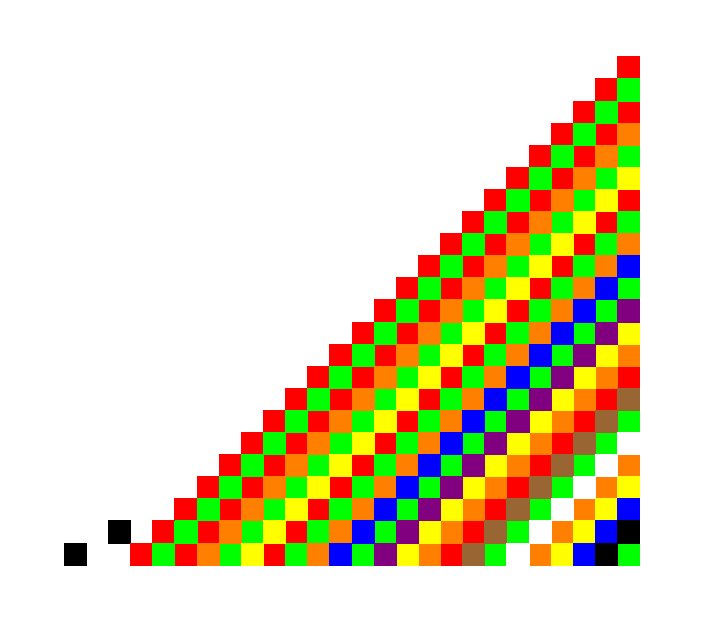

```mathematica
Show[Graphics[{Rectangle[{0,1}],Rectangle[{2,2}]}],Graphics@flatRectProto]
```

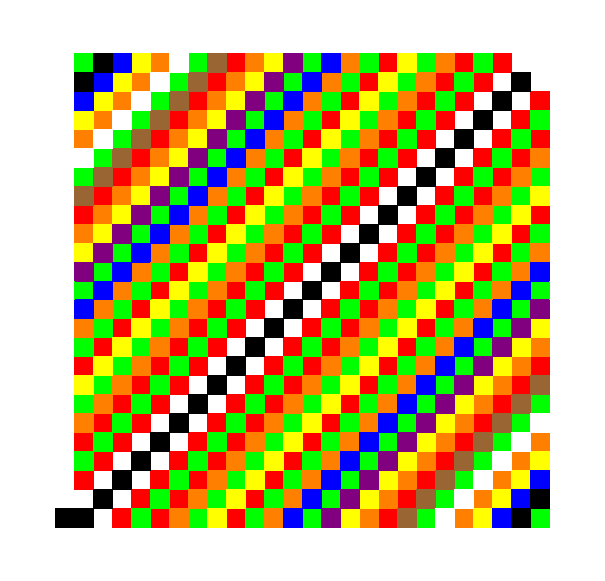

Part::partw: Part 145 of {{3,1},{4,2},{5,1},{5,3},{6,2},{6,4},{7,1},{7,3},{7,5},{8,2},«134»} does not exist.

Part::partw: Part 146 of {{3,1},{4,2},{5,1},{5,3},{6,2},{6,4},{7,1},{7,3},{7,5},{8,2},«134»} does not exist.

Part::partw: Part 147 of {{3,1},{4,2},{5,1},{5,3},{6,2},{6,4},{7,1},{7,3},{7,5},{8,2},«134»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
Show[Graphics[{Rectangle[{0,1}],Rectangle[{2,2}]}],Graphics@flatRect]
```

{{RGBColor[1, 0, 0],Rectangle[{3,1}]},{RGBColor[1, 0, 0],Rectangle[{4,2}]},{RGBColor[1, 0, 0],Rectangle[{5,1}]},{RGBColor[1, 0, 0],Rectangle[{5,3}]},{RGBColor[1, 0, 0],Rectangle[{6,2}]},{RGBColor[1, 0, 0],Rectangle[{6,4}]},{RGBColor[1, 0, 0],Rectangle[{7,1}]},{RGBColor[1, 0, 0],Rectangle[{7,3}]},{RGBColor[1, 0, 0],Rectangle[{7,5}]},{RGBColor[1, 0, 0],Rectangle[{8,2}]},{RGBColor[1, 0, 0],Rectangle[{8,4}]},{RGBColor[1, 0, 0],Rectangle[{8,6}]},{RGBColor[1, 0, 0],Rectangle[{9,1}]},{RGBColor[1, 0, 0],Rectangle[{9,3}]},{RGBColor[1, 0, 0],Rectangle[{9,5}]},{RGBColor[1, 0, 0],Rectangle[{9,7}]},{RGBColor[1, 0, 0],Rectangle[{10,2}]},{RGBColor[1, 0, 0],Rectangle[{10,4}]},{RGBColor[1, 0, 0],Rectangle[{10,6}]},{RGBColor[1, 0, 0],Rectangle[{10,8}]},{RGBColor[1, 0, 0],Rectangle[{11,1}]},{RGBColor[1, 0, 0],Rectangle[{11,3}]},{RGBColor[1, 0, 0],Rectangle[{11,5}]},{RGBColor[1, 0, 0],Rectangle[{11,7}]},{RGBColor[1, 0, 0],Rectangle[{11,9}]},{RGBColor[1, 0, 0],Rectangle[{12,2}]},{RGBColor[1, 0, 0],Rectangle[{12,4}]},{RGBColor[1, 0, 0],Rectangle[{12,6}]},{RGBColor[1, 0, 0],Rectangle[{12,8}]},{RGBColor[1, 0, 0],Rectangle[{12,10}]},{RGBColor[1, 0, 0],Rectangle[{13,1}]},{RGBColor[1, 0, 0],Rectangle[{13,3}]},{RGBColor[1, 0, 0],Rectangle[{13,5}]},{RGBColor[1, 0, 0],Rectangle[{13,7}]},{RGBColor[1, 0, 0],Rectangle[{13,9}]},{RGBColor[1, 0, 0],Rectangle[{13,11}]},{RGBColor[1, 0, 0],Rectangle[{14,2}]},{RGBColor[1, 0, 0],Rectangle[{14,4}]},{RGBColor[1, 0, 0],Rectangle[{14,6}]},{RGBColor[1, 0, 0],Rectangle[{14,8}]},{RGBColor[1, 0, 0],Rectangle[{14,10}]},{RGBColor[1, 0, 0],Rectangle[{14,12}]},{RGBColor[1, 0, 0],Rectangle[{15,1}]},{RGBColor[1, 0, 0],Rectangle[{15,3}]},{RGBColor[1, 0, 0],Rectangle[{15,5}]},{RGBColor[1, 0, 0],Rectangle[{15,7}]},{RGBColor[1, 0, 0],Rectangle[{15,9}]},{RGBColor[1, 0, 0],Rectangle[{15,11}]},{RGBColor[1, 0, 0],Rectangle[{15,13}]},{RGBColor[1, 0, 0],Rectangle[{16,2}]},{RGBColor[1, 0, 0],Rectangle[{16,4}]},{RGBColor[1, 0, 0],Rectangle[{16,6}]},{RGBColor[1, 0, 0],Rectangle[{16,8}]},{RGBColor[1, 0, 0],Rectangle[{16,10}]},{RGBColor[1, 0, 0],Rectangle[{16,12}]},{RGBColor[1, 0, 0],Rectangle[{16,14}]},{RGBColor[1, 0, 0],Rectangle[{17,1}]},{RGBColor[1, 0, 0],Rectangle[{17,3}]},{RGBColor[1, 0, 0],Rectangle[{17,5}]},{RGBColor[1, 0, 0],Rectangle[{17,7}]},{RGBColor[1, 0, 0],Rectangle[{17,9}]},{RGBColor[1, 0, 0],Rectangle[{17,11}]},{RGBColor[1, 0, 0],Rectangle[{17,13}]},{RGBColor[1, 0, 0],Rectangle[{17,15}]},{RGBColor[1, 0, 0],Rectangle[{18,2}]},{RGBColor[1, 0, 0],Rectangle[{18,4}]},{RGBColor[1, 0, 0],Rectangle[{18,6}]},{RGBColor[1, 0, 0],Rectangle[{18,8}]},{RGBColor[1, 0, 0],Rectangle[{18,10}]},{RGBColor[1, 0, 0],Rectangle[{18,12}]},{RGBColor[1, 0, 0],Rectangle[{18,14}]},{RGBColor[1, 0, 0],Rectangle[{18,16}]},{RGBColor[1, 0, 0],Rectangle[{19,1}]},{RGBColor[1, 0, 0],Rectangle[{19,3}]},{RGBColor[1, 0, 0],Rectangle[{19,5}]},{RGBColor[1, 0, 0],Rectangle[{19,7}]},{RGBColor[1, 0, 0],Rectangle[{19,9}]},{RGBColor[1, 0, 0],Rectangle[{19,11}]},{RGBColor[1, 0, 0],Rectangle[{19,13}]},{RGBColor[1, 0, 0],Rectangle[{19,15}]},{RGBColor[1, 0, 0],Rectangle[{19,17}]},{RGBColor[1, 0, 0],Rectangle[{20,2}]},{RGBColor[1, 0, 0],Rectangle[{20,4}]},{RGBColor[1, 0, 0],Rectangle[{20,6}]},{RGBColor[1, 0, 0],Rectangle[{20,8}]},{RGBColor[1, 0, 0],Rectangle[{20,10}]},{RGBColor[1, 0, 0],Rectangle[{20,12}]},{RGBColor[1, 0, 0],Rectangle[{20,14}]},{RGBColor[1, 0, 0],Rectangle[{20,16}]},{RGBColor[1, 0, 0],Rectangle[{20,18}]},{RGBColor[1, 0, 0],Rectangle[{21,1}]},{RGBColor[1, 0, 0],Rectangle[{21,3}]},{RGBColor[1, 0, 0],Rectangle[{21,5}]},{RGBColor[1, 0, 0],Rectangle[{21,7}]},{RGBColor[1, 0, 0],Rectangle[{21,9}]},{RGBColor[1, 0, 0],Rectangle[{21,11}]},{RGBColor[1, 0, 0],Rectangle[{21,13}]},{RGBColor[1, 0, 0],Rectangle[{21,15}]},{RGBColor[1, 0, 0],Rectangle[{21,17}]},{RGBColor[1, 0, 0],Rectangle[{21,19}]},{RGBColor[1, 0, 0],Rectangle[{22,2}]},{RGBColor[1, 0, 0],Rectangle[{22,4}]},{RGBColor[1, 0, 0],Rectangle[{22,6}]},{RGBColor[1, 0, 0],Rectangle[{22,8}]},{RGBColor[1, 0, 0],Rectangle[{22,10}]},{RGBColor[1, 0, 0],Rectangle[{22,12}]},{RGBColor[1, 0, 0],Rectangle[{22,14}]},{RGBColor[1, 0, 0],Rectangle[{22,16}]},{RGBColor[1, 0, 0],Rectangle[{22,18}]},{RGBColor[1, 0, 0],Rectangle[{22,20}]},{RGBColor[1, 0, 0],Rectangle[{23,1}]},{RGBColor[1, 0, 0],Rectangle[{23,3}]},{RGBColor[1, 0, 0],Rectangle[{23,5}]},{RGBColor[1, 0, 0],Rectangle[{23,7}]},{RGBColor[1, 0, 0],Rectangle[{23,9}]},{RGBColor[1, 0, 0],Rectangle[{23,11}]},{RGBColor[1, 0, 0],Rectangle[{23,13}]},{RGBColor[1, 0, 0],Rectangle[{23,15}]},{RGBColor[1, 0, 0],Rectangle[{23,17}]},{RGBColor[1, 0, 0],Rectangle[{23,19}]},{RGBColor[1, 0, 0],Rectangle[{23,21}]},{RGBColor[1, 0, 0],Rectangle[{24,2}]},{RGBColor[1, 0, 0],Rectangle[{24,4}]},{RGBColor[1, 0, 0],Rectangle[{24,6}]},{RGBColor[1, 0, 0],Rectangle[{24,8}]},{RGBColor[1, 0, 0],Rectangle[{24,10}]},{RGBColor[1, 0, 0],Rectangle[{24,12}]},{RGBColor[1, 0, 0],Rectangle[{24,14}]},{RGBColor[1, 0, 0],Rectangle[{24,16}]},{RGBColor[1, 0, 0],Rectangle[{24,18}]},{RGBColor[1, 0, 0],Rectangle[{24,20}]},{RGBColor[1, 0, 0],Rectangle[{24,22}]},{RGBColor[1, 0, 0],Rectangle[{25,1}]},{RGBColor[1, 0, 0],Rectangle[{25,3}]},{RGBColor[1, 0, 0],Rectangle[{25,5}]},{RGBColor[1, 0, 0],Rectangle[{25,7}]},{RGBColor[1, 0, 0],Rectangle[{25,9}]},{RGBColor[1, 0, 0],Rectangle[{25,11}]},{RGBColor[1, 0, 0],Rectangle[{25,13}]},{RGBColor[1, 0, 0],Rectangle[{25,15}]},{RGBColor[1, 0, 0],Rectangle[{25,17}]},{RGBColor[1, 0, 0],Rectangle[{25,19}]},{RGBColor[1, 0, 0],Rectangle[{25,21}]},{RGBColor[1, 0, 0],Rectangle[{25,23}]},{RGBColor[1, 0, 0],Rectangle[{4,1}]},{RGBColor[1, 0, 0],Rectangle[{5,2}]},{RGBColor[1, 0, 0],Rectangle[{6,3}]},{RGBColor[1, 0, 0],Rectangle[{7,1}]},{RGBColor[1, 0, 0],Rectangle[{7,4}]},{RGBColor[1, 0, 0],Rectangle[{8,2}]},{RGBColor[1, 0, 0],Rectangle[{8,5}]},{RGBColor[1, 0, 0],Rectangle[{9,3}]},{RGBColor[1, 0, 0],Rectangle[{9,6}]},{RGBColor[1, 0, 0],Rectangle[{10,1}]},{RGBColor[1, 0, 0],Rectangle[{10,4}]},{RGBColor[1, 0, 0],Rectangle[{10,7}]},{RGBColor[1, 0, 0],Rectangle[{11,2}]},{RGBColor[1, 0, 0],Rectangle[{11,5}]},{RGBColor[1, 0, 0],Rectangle[{11,8}]},{RGBColor[1, 0, 0],Rectangle[{12,3}]},{RGBColor[1, 0, 0],Rectangle[{12,6}]},{RGBColor[1, 0, 0],Rectangle[{12,9}]},{RGBColor[1, 0, 0],Rectangle[{13,1}]},{RGBColor[1, 0, 0],Rectangle[{13,4}]},{RGBColor[1, 0, 0],Rectangle[{13,7}]},{RGBColor[1, 0, 0],Rectangle[{13,10}]},{RGBColor[1, 0, 0],Rectangle[{14,2}]},{RGBColor[1, 0, 0],Rectangle[{14,5}]},{RGBColor[1, 0, 0],Rectangle[{14,8}]},{RGBColor[1, 0, 0],Rectangle[{14,11}]},{RGBColor[1, 0, 0],Rectangle[{15,3}]},{RGBColor[1, 0, 0],Rectangle[{15,6}]},{RGBColor[1, 0, 0],Rectangle[{15,9}]},{RGBColor[1, 0, 0],Rectangle[{15,12}]},{RGBColor[1, 0, 0],Rectangle[{16,1}]},{RGBColor[1, 0, 0],Rectangle[{16,4}]},{RGBColor[1, 0, 0],Rectangle[{16,7}]},{RGBColor[1, 0, 0],Rectangle[{16,10}]},{RGBColor[1, 0, 0],Rectangle[{16,13}]},{RGBColor[1, 0, 0],Rectangle[{17,2}]},{RGBColor[1, 0, 0],Rectangle[{17,5}]},{RGBColor[1, 0, 0],Rectangle[{17,8}]},{RGBColor[1, 0, 0],Rectangle[{17,11}]},{RGBColor[1, 0, 0],Rectangle[{17,14}]},{RGBColor[1, 0, 0],Rectangle[{18,3}]},{RGBColor[1, 0, 0],Rectangle[{18,6}]},{RGBColor[1, 0, 0],Rectangle[{18,9}]},{RGBColor[1, 0, 0],Rectangle[{18,12}]},{RGBColor[1, 0, 0],Rectangle[{18,15}]},{RGBColor[1, 0, 0],Rectangle[{19,1}]},{RGBColor[1, 0, 0],Rectangle[{19,4}]},{RGBColor[1, 0, 0],Rectangle[{19,7}]},{RGBColor[1, 0, 0],Rectangle[{19,10}]},{RGBColor[1, 0, 0],Rectangle[{19,13}]},{RGBColor[1, 0, 0],Rectangle[{19,16}]},{RGBColor[1, 0, 0],Rectangle[{20,2}]},{RGBColor[1, 0, 0],Rectangle[{20,5}]},{RGBColor[1, 0, 0],Rectangle[{20,8}]},{RGBColor[1, 0, 0],Rectangle[{20,11}]},{RGBColor[1, 0, 0],Rectangle[{20,14}]},{RGBColor[1, 0, 0],Rectangle[{20,17}]},{RGBColor[1, 0, 0],Rectangle[{21,3}]},{RGBColor[1, 0, 0],Rectangle[{21,6}]},{RGBColor[1, 0, 0],Rectangle[{21,9}]},{RGBColor[1, 0, 0],Rectangle[{21,12}]},{RGBColor[1, 0, 0],Rectangle[{21,15}]},{RGBColor[1, 0, 0],Rectangle[{21,18}]},{RGBColor[1, 0, 0],Rectangle[{22,1}]},{RGBColor[1, 0, 0],Rectangle[{22,4}]},{RGBColor[1, 0, 0],Rectangle[{22,7}]},{RGBColor[1, 0, 0],Rectangle[{22,10}]},{RGBColor[1, 0, 0],Rectangle[{22,13}]},{RGBColor[1, 0, 0],Rectangle[{22,16}]},{RGBColor[1, 0, 0],Rectangle[{22,19}]},{RGBColor[1, 0, 0],Rectangle[{23,2}]},{RGBColor[1, 0, 0],Rectangle[{23,5}]},{RGBColor[1, 0, 0],Rectangle[{23,8}]},{RGBColor[1, 0, 0],Rectangle[{23,11}]},{RGBColor[1, 0, 0],Rectangle[{23,14}]},{RGBColor[1, 0, 0],Rectangle[{23,17}]},{RGBColor[1, 0, 0],Rectangle[{23,20}]},{RGBColor[1, 0, 0],Rectangle[{24,3}]},{RGBColor[1, 0, 0],Rectangle[{24,6}]},{RGBColor[1, 0, 0],Rectangle[{24,9}]},{RGBColor[1, 0, 0],Rectangle[{24,12}]},{RGBColor[1, 0, 0],Rectangle[{24,15}]},{RGBColor[1, 0, 0],Rectangle[{24,18}]},{RGBColor[1, 0, 0],Rectangle[{24,21}]},{RGBColor[1, 0, 0],Rectangle[{25,1}]},{RGBColor[1, 0, 0],Rectangle[{25,4}]},{RGBColor[1, 0, 0],Rectangle[{25,7}]},{RGBColor[1, 0, 0],Rectangle[{25,10}]},{RGBColor[1, 0, 0],Rectangle[{25,13}]},{RGBColor[1, 0, 0],Rectangle[{25,16}]},{RGBColor[1, 0, 0],Rectangle[{25,19}]},{RGBColor[1, 0, 0],Rectangle[{25,22}]},{RGBColor[1, 0, 0],Rectangle[{6,1}]},{RGBColor[1, 0, 0],Rectangle[{7,2}]},{RGBColor[1, 0, 0],Rectangle[{8,3}]},{RGBColor[1, 0, 0],Rectangle[{9,4}]},{RGBColor[1, 0, 0],Rectangle[{10,5}]},{RGBColor[1, 0, 0],Rectangle[{11,1}]},{RGBColor[1, 0, 0],Rectangle[{11,6}]},{RGBColor[1, 0, 0],Rectangle[{12,2}]},{RGBColor[1, 0, 0],Rectangle[{12,7}]},{RGBColor[1, 0, 0],Rectangle[{13,3}]},{RGBColor[1, 0, 0],Rectangle[{13,8}]},{RGBColor[1, 0, 0],Rectangle[{14,4}]},{RGBColor[1, 0, 0],Rectangle[{14,9}]},{RGBColor[1, 0, 0],Rectangle[{15,5}]},{RGBColor[1, 0, 0],Rectangle[{15,10}]},{RGBColor[1, 0, 0],Rectangle[{16,1}]},{RGBColor[1, 0, 0],Rectangle[{16,6}]},{RGBColor[1, 0, 0],Rectangle[{16,11}]},{RGBColor[1, 0, 0],Rectangle[{17,2}]},{RGBColor[1, 0, 0],Rectangle[{17,7}]},{RGBColor[1, 0, 0],Rectangle[{17,12}]},{RGBColor[1, 0, 0],Rectangle[{18,3}]},{RGBColor[1, 0, 0],Rectangle[{18,8}]},{RGBColor[1, 0, 0],Rectangle[{18,13}]},{RGBColor[1, 0, 0],Rectangle[{19,4}]},{RGBColor[1, 0, 0],Rectangle[{19,9}]},{RGBColor[1, 0, 0],Rectangle[{19,14}]},{RGBColor[1, 0, 0],Rectangle[{20,5}]},{RGBColor[1, 0, 0],Rectangle[{20,10}]},{RGBColor[1, 0, 0],Rectangle[{20,15}]},{RGBColor[1, 0, 0],Rectangle[{21,1}]},{RGBColor[1, 0, 0],Rectangle[{21,6}]},{RGBColor[1, 0, 0],Rectangle[{21,11}]},{RGBColor[1, 0, 0],Rectangle[{21,16}]},{RGBColor[1, 0, 0],Rectangle[{22,2}]},{RGBColor[1, 0, 0],Rectangle[{22,7}]},{RGBColor[1, 0, 0],Rectangle[{22,12}]},{RGBColor[1, 0, 0],Rectangle[{22,17}]},{RGBColor[1, 0, 0],Rectangle[{23,3}]},{RGBColor[1, 0, 0],Rectangle[{23,8}]},{RGBColor[1, 0, 0],Rectangle[{23,13}]},{RGBColor[1, 0, 0],Rectangle[{23,18}]},{RGBColor[1, 0, 0],Rectangle[{24,4}]},{RGBColor[1, 0, 0],Rectangle[{24,9}]},{RGBColor[1, 0, 0],Rectangle[{24,14}]},{RGBColor[1, 0, 0],Rectangle[{24,19}]},{RGBColor[1, 0, 0],Rectangle[{25,5}]},{RGBColor[1, 0, 0],Rectangle[{25,10}]},{RGBColor[1, 0, 0],Rectangle[{25,15}]},{RGBColor[1, 0, 0],Rectangle[{25,20}]},{RGBColor[1, 0, 0],Rectangle[{8,1}]},{RGBColor[1, 0, 0],Rectangle[{9,2}]},{RGBColor[1, 0, 0],Rectangle[{10,3}]},{RGBColor[1, 0, 0],Rectangle[{11,4}]},{RGBColor[1, 0, 0],Rectangle[{12,5}]},{RGBColor[1, 0, 0],Rectangle[{13,6}]},{RGBColor[1, 0, 0],Rectangle[{14,7}]},{RGBColor[1, 0, 0],Rectangle[{15,1}]},{RGBColor[1, 0, 0],Rectangle[{15,8}]},{RGBColor[1, 0, 0],Rectangle[{16,2}]},{RGBColor[1, 0, 0],Rectangle[{16,9}]},{RGBColor[1, 0, 0],Rectangle[{17,3}]},{RGBColor[1, 0, 0],Rectangle[{17,10}]},{RGBColor[1, 0, 0],Rectangle[{18,4}]},{RGBColor[1, 0, 0],Rectangle[{18,11}]},{RGBColor[1, 0, 0],Rectangle[{19,5}]},{RGBColor[1, 0, 0],Rectangle[{19,12}]},{RGBColor[1, 0, 0],Rectangle[{20,6}]},{RGBColor[1, 0, 0],Rectangle[{20,13}]},{RGBColor[1, 0, 0],Rectangle[{21,7}]},{RGBColor[1, 0, 0],Rectangle[{21,14}]},{RGBColor[1, 0, 0],Rectangle[{22,1}]},{RGBColor[1, 0, 0],Rectangle[{22,8}]},{RGBColor[1, 0, 0],Rectangle[{22,15}]},{RGBColor[1, 0, 0],Rectangle[{23,2}]},{RGBColor[1, 0, 0],Rectangle[{23,9}]},{RGBColor[1, 0, 0],Rectangle[{23,16}]},{RGBColor[1, 0, 0],Rectangle[{24,3}]},{RGBColor[1, 0, 0],Rectangle[{24,10}]},{RGBColor[1, 0, 0],Rectangle[{24,17}]},{RGBColor[1, 0, 0],Rectangle[{25,4}]},{RGBColor[1, 0, 0],Rectangle[{25,11}]},{RGBColor[1, 0, 0],Rectangle[{25,18}]},{RGBColor[1, 0, 0],Rectangle[{12,1}]},{RGBColor[1, 0, 0],Rectangle[{13,2}]},{RGBColor[1, 0, 0],Rectangle[{14,3}]},{RGBColor[1, 0, 0],Rectangle[{15,4}]},{RGBColor[1, 0, 0],Rectangle[{16,5}]},{RGBColor[1, 0, 0],Rectangle[{17,6}]},{RGBColor[1, 0, 0],Rectangle[{18,7}]},{RGBColor[1, 0, 0],Rectangle[{19,8}]},{RGBColor[1, 0, 0],Rectangle[{20,9}]},{RGBColor[1, 0, 0],Rectangle[{21,10}]},{RGBColor[1, 0, 0],Rectangle[{22,11}]},{RGBColor[1, 0, 0],Rectangle[{23,1}]},{RGBColor[1, 0, 0],Rectangle[{23,12}]},{RGBColor[1, 0, 0],Rectangle[{24,2}]},{RGBColor[1, 0, 0],Rectangle[{24,13}]},{RGBColor[1, 0, 0],Rectangle[{25,3}]},{RGBColor[1, 0, 0],Rectangle[{25,14}]},{RGBColor[1, 0, 0],Rectangle[{14,1}]},{RGBColor[1, 0, 0],Rectangle[{15,2}]},{RGBColor[1, 0, 0],Rectangle[{16,3}]},{RGBColor[1, 0, 0],Rectangle[{17,4}]},{RGBColor[1, 0, 0],Rectangle[{18,5}]},{RGBColor[1, 0, 0],Rectangle[{19,6}]},{RGBColor[1, 0, 0],Rectangle[{20,7}]},{RGBColor[1, 0, 0],Rectangle[{21,8}]},{RGBColor[1, 0, 0],Rectangle[{22,9}]},{RGBColor[1, 0, 0],Rectangle[{23,10}]},{RGBColor[1, 0, 0],Rectangle[{24,11}]},{RGBColor[1, 0, 0],Rectangle[{25,12}]},{RGBColor[1, 0, 0],Rectangle[{18,1}]},{RGBColor[1, 0, 0],Rectangle[{19,2}]},{RGBColor[1, 0, 0],Rectangle[{20,3}]},{RGBColor[1, 0, 0],Rectangle[{21,4}]},{RGBColor[1, 0, 0],Rectangle[{22,5}]},{RGBColor[1, 0, 0],Rectangle[{23,6}]},{RGBColor[1, 0, 0],Rectangle[{24,7}]},{RGBColor[1, 0, 0],Rectangle[{25,8}]},{RGBColor[1, 0, 0],Rectangle[{20,1}]},{RGBColor[1, 0, 0],Rectangle[{21,2}]},{RGBColor[1, 0, 0],Rectangle[{22,3}]},{RGBColor[1, 0, 0],Rectangle[{23,4}]},{RGBColor[1, 0, 0],Rectangle[{24,5}]},{RGBColor[1, 0, 0],Rectangle[{25,6}]},{RGBColor[1, 0, 0],Rectangle[{24,1}]},{RGBColor[1, 0, 0],Rectangle[{25,2}]}}

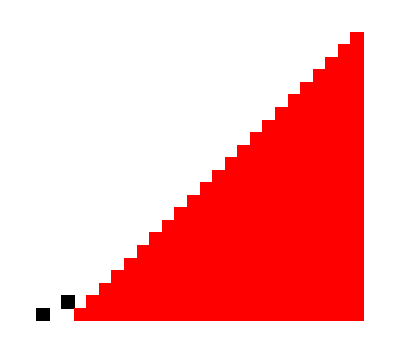

```mathematica
rectangles:=Table[{Red,Rectangle[flattenedResult25and10PrimesFromFunc[[i]]]},{i,1,Length@flattenedResult25and10PrimesFromFunc}]
(*AppendTo[rectangles,{Red,Rectangle[{0,0}]}]*)
(*AppendTo[rectangles,{Green,Rectangle[{0,0}]}*)

rectangles
(*Graphics@rectangles*)
Show[Graphics[{Rectangle[{0,1}],Rectangle[{2,2}]}],Graphics@rectangles]
```

```mathematica
result25and10Primes[[1]][[1]]
result25and10Primes[[1]]
```

{{3,1},{4,2},{5,1},{5,3},{6,2},{6,4},{7,1},{7,3},{7,5},{8,2},{8,4},{8,6},{9,1},{9,3},{9,5},{9,7},{10,2},{10,4},{10,6},{10,8},{11,1},{11,3},{11,5},{11,7},{11,9},{12,2},{12,4},{12,6},{12,8},{12,10},{13,1},{13,3},{13,5},{13,7},{13,9},{13,11},{14,2},{14,4},{14,6},{14,8},{14,10},{14,12},{15,1},{15,3},{15,5},{15,7},{15,9},{15,11},{15,13},{16,2},{16,4},{16,6},{16,8},{16,10},{16,12},{16,14},{17,1},{17,3},{17,5},{17,7},{17,9},{17,11},{17,13},{17,15},{18,2},{18,4},{18,6},{18,8},{18,10},{18,12},{18,14},{18,16},{19,1},{19,3},{19,5},{19,7},{19,9},{19,11},{19,13},{19,15},{19,17},{20,2},{20,4},{20,6},{20,8},{20,10},{20,12},{20,14},{20,16},{20,18},{21,1},{21,3},{21,5},{21,7},{21,9},{21,11},{21,13},{21,15},{21,17},{21,19},{22,2},{22,4},{22,6},{22,8},{22,10},{22,12},{22,14},{22,16},{22,18},{22,20},{23,1},{23,3},{23,5},{23,7},{23,9},{23,11},{23,13},{23,15},{23,17},{23,19},{23,21},{24,2},{24,4},{24,6},{24,8},{24,10},{24,12},{24,14},{24,16},{24,18},{24,20},{24,22},{25,1},{25,3},{25,5},{25,7},{25,9},{25,11},{25,13},{25,15},{25,17},{25,19},{25,21},{25,23}}

{{{3,1},{4,2},{5,1},{5,3},{6,2},{6,4},{7,1},{7,3},{7,5},{8,2},{8,4},{8,6},{9,1},{9,3},{9,5},{9,7},{10,2},{10,4},{10,6},{10,8},{11,1},{11,3},{11,5},{11,7},{11,9},{12,2},{12,4},{12,6},{12,8},{12,10},{13,1},{13,3},{13,5},{13,7},{13,9},{13,11},{14,2},{14,4},{14,6},{14,8},{14,10},{14,12},{15,1},{15,3},{15,5},{15,7},{15,9},{15,11},{15,13},{16,2},{16,4},{16,6},{16,8},{16,10},{16,12},{16,14},{17,1},{17,3},{17,5},{17,7},{17,9},{17,11},{17,13},{17,15},{18,2},{18,4},{18,6},{18,8},{18,10},{18,12},{18,14},{18,16},{19,1},{19,3},{19,5},{19,7},{19,9},{19,11},{19,13},{19,15},{19,17},{20,2},{20,4},{20,6},{20,8},{20,10},{20,12},{20,14},{20,16},{20,18},{21,1},{21,3},{21,5},{21,7},{21,9},{21,11},{21,13},{21,15},{21,17},{21,19},{22,2},{22,4},{22,6},{22,8},{22,10},{22,12},{22,14},{22,16},{22,18},{22,20},{23,1},{23,3},{23,5},{23,7},{23,9},{23,11},{23,13},{23,15},{23,17},{23,19},{23,21},{24,2},{24,4},{24,6},{24,8},{24,10},{24,12},{24,14},{24,16},{24,18},{24,20},{24,22},{25,1},{25,3},{25,5},{25,7},{25,9},{25,11},{25,13},{25,15},{25,17},{25,19},{25,21},{25,23}}}

```mathematica
binaryListComparator[listA_,listB_]:=
And[
listA[[1]]==listB[[1]],
listA[[2]]==listB[[2]]
]
```

```mathematica
actualFlatten[nLengths_,collectionNOfLists_]:=
Module[
{flattened={}},
{
For[
i=1,
i<Length[nLengths],
i++,
{
For[
j=1,
j<nLengths[[i]],
j++,
AppendTo[flattened,]
]
}
]
}
]
```

```mathematica
binaryListComparator[{0,1},{0,1}]
```

True

```mathematica
binaryListComparator[listA_,listB_]:=
Module[
{},
If[
And[
listA[[1]]==listB[[1]],
listA[[2]]==listB[[2]]
],
{}
]
]
(*TO-DO: consolodiate all custom-functions into a central location, the goal is to import this file, and access all of these functions *)
```

```mathematica
result25and10Primes;
```

```mathematica
repeats={}
left={}
right=result25and10Primes
```

```mathematica
Length@result25and10Primes
```

10

```mathematica
result2 = congruenceModN[foo,2]
```

{{{3,1},{4,2},{5,1},{5,3},{6,2},{6,4},{7,1},{7,3},{7,5},{8,2},{8,4},{8,6},{9,1},{9,3},{9,5},{9,7},{10,2},{10,4},{10,6},{10,8},{11,1},{11,3},{11,5},{11,7},{11,9},{12,2},{12,4},{12,6},{12,8},{12,10},{13,1},{13,3},{13,5},{13,7},{13,9},{13,11},{14,2},{14,4},{14,6},{14,8},{14,10},{14,12},{15,1},{15,3},{15,5},{15,7},{15,9},{15,11},{15,13},{16,2},{16,4},{16,6},{16,8},{16,10},{16,12},{16,14},{17,1},{17,3},{17,5},{17,7},{17,9},{17,11},{17,13},{17,15},{18,2},{18,4},{18,6},{18,8},{18,10},{18,12},{18,14},{18,16},{19,1},{19,3},{19,5},{19,7},{19,9},{19,11},{19,13},{19,15},{19,17},{20,2},{20,4},{20,6},{20,8},{20,10},{20,12},{20,14},{20,16},{20,18},{21,1},{21,3},{21,5},{21,7},{21,9},{21,11},{21,13},{21,15},{21,17},{21,19},{22,2},{22,4},{22,6},{22,8},{22,10},{22,12},{22,14},{22,16},{22,18},{22,20},{23,1},{23,3},{23,5},{23,7},{23,9},{23,11},{23,13},{23,15},{23,17},{23,19},{23,21},{24,2},{24,4},{24,6},{24,8},{24,10},{24,12},{24,14},{24,16},{24,18},{24,20},{24,22},{25,1},{25,3},{25,5},{25,7},{25,9},{25,11},{25,13},{25,15},{25,17},{25,19},{25,21},{25,23},{26,2},{26,4},{26,6},{26,8},{26,10},{26,12},{26,14},{26,16},{26,18},{26,20},{26,22},{26,24},{27,1},{27,3},{27,5},{27,7},{27,9},{27,11},{27,13},{27,15},{27,17},{27,19},{27,21},{27,23},{27,25},{28,2},{28,4},{28,6},{28,8},{28,10},{28,12},{28,14},{28,16},{28,18},{28,20},{28,22},{28,24},{28,26},{29,1},{29,3},{29,5},{29,7},{29,9},{29,11},{29,13},{29,15},{29,17},{29,19},{29,21},{29,23},{29,25},{29,27},{30,2},{30,4},{30,6},{30,8},{30,10},{30,12},{30,14},{30,16},{30,18},{30,20},{30,22},{30,24},{30,26},{30,28},{31,1},{31,3},{31,5},{31,7},{31,9},{31,11},{31,13},{31,15},{31,17},{31,19},{31,21},{31,23},{31,25},{31,27},{31,29},{32,2},{32,4},{32,6},{32,8},{32,10},{32,12},{32,14},{32,16},{32,18},{32,20},{32,22},{32,24},{32,26},{32,28},{32,30},{33,1},{33,3},{33,5},{33,7},{33,9},{33,11},{33,13},{33,15},{33,17},{33,19},{33,21},{33,23},{33,25},{33,27},{33,29},{33,31},{34,2},{34,4},{34,6},{34,8},{34,10},{34,12},{34,14},{34,16},{34,18},{34,20},{34,22},{34,24},{34,26},{34,28},{34,30},{34,32},{35,1},{35,3},{35,5},{35,7},{35,9},{35,11},{35,13},{35,15},{35,17},{35,19},{35,21},{35,23},{35,25},{35,27},{35,29},{35,31},{35,33},{36,2},{36,4},{36,6},{36,8},{36,10},{36,12},{36,14},{36,16},{36,18},{36,20},{36,22},{36,24},{36,26},{36,28},{36,30},{36,32},{36,34},{37,1},{37,3},{37,5},{37,7},{37,9},{37,11},{37,13},{37,15},{37,17},{37,19},{37,21},{37,23},{37,25},{37,27},{37,29},{37,31},{37,33},{37,35},{38,2},{38,4},{38,6},{38,8},{38,10},{38,12},{38,14},{38,16},{38,18},{38,20},{38,22},{38,24},{38,26},{38,28},{38,30},{38,32},{38,34},{38,36},{39,1},{39,3},{39,5},{39,7},{39,9},{39,11},{39,13},{39,15},{39,17},{39,19},{39,21},{39,23},{39,25},{39,27},{39,29},{39,31},{39,33},{39,35},{39,37},{40,2},{40,4},{40,6},{40,8},{40,10},{40,12},{40,14},{40,16},{40,18},{40,20},{40,22},{40,24},{40,26},{40,28},{40,30},{40,32},{40,34},{40,36},{40,38},{41,1},{41,3},{41,5},{41,7},{41,9},{41,11},{41,13},{41,15},{41,17},{41,19},{41,21},{41,23},{41,25},{41,27},{41,29},{41,31},{41,33},{41,35},{41,37},{41,39},{42,2},{42,4},{42,6},{42,8},{42,10},{42,12},{42,14},{42,16},{42,18},{42,20},{42,22},{42,24},{42,26},{42,28},{42,30},{42,32},{42,34},{42,36},{42,38},{42,40},{43,1},{43,3},{43,5},{43,7},{43,9},{43,11},{43,13},{43,15},{43,17},{43,19},{43,21},{43,23},{43,25},{43,27},{43,29},{43,31},{43,33},{43,35},{43,37},{43,39},{43,41},{44,2},{44,4},{44,6},{44,8},{44,10},{44,12},{44,14},{44,16},{44,18},{44,20},{44,22},{44,24},{44,26},{44,28},{44,30},{44,32},{44,34},{44,36},{44,38},{44,40},{44,42},{45,1},{45,3},{45,5},{45,7},{45,9},{45,11},{45,13},{45,15},{45,17},{45,19},{45,21},{45,23},{45,25},{45,27},{45,29},{45,31},{45,33},{45,35},{45,37},{45,39},{45,41},{45,43},{46,2},{46,4},{46,6},{46,8},{46,10},{46,12},{46,14},{46,16},{46,18},{46,20},{46,22},{46,24},{46,26},{46,28},{46,30},{46,32},{46,34},{46,36},{46,38},{46,40},{46,42},{46,44},{47,1},{47,3},{47,5},{47,7},{47,9},{47,11},{47,13},{47,15},{47,17},{47,19},{47,21},{47,23},{47,25},{47,27},{47,29},{47,31},{47,33},{47,35},{47,37},{47,39},{47,41},{47,43},{47,45},{48,2},{48,4},{48,6},{48,8},{48,10},{48,12},{48,14},{48,16},{48,18},{48,20},{48,22},{48,24},{48,26},{48,28},{48,30},{48,32},{48,34},{48,36},{48,38},{48,40},{48,42},{48,44},{48,46},{49,1},{49,3},{49,5},{49,7},{49,9},{49,11},{49,13},{49,15},{49,17},{49,19},{49,21},{49,23},{49,25},{49,27},{49,29},{49,31},{49,33},{49,35},{49,37},{49,39},{49,41},{49,43},{49,45},{49,47},{50,2},{50,4},{50,6},{50,8},{50,10},{50,12},{50,14},{50,16},{50,18},{50,20},{50,22},{50,24},{50,26},{50,28},{50,30},{50,32},{50,34},{50,36},{50,38},{50,40},{50,42},{50,44},{50,46},{50,48}}}

```mathematica
{{{1,1},{1,3},{1,5},{1,7},{1,9},{1,11},{1,13},{1,15},{1,17},{1,19},{1,21},{1,23},{1,25},{1,27},{1,29},{1,31},{1,33},{1,35},{1,37},{1,39},{1,41},{1,43},{1,45},{1,47},{1,49},{2,2},{2,4},{2,6},{2,8},{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{2,24},{2,26},{2,28},{2,30},{2,32},{2,34},{2,36},{2,38},{2,40},{2,42},{2,44},{2,46},{2,48},{2,50},{3,1},{3,3},{3,5},{3,7},{3,9},{3,11},{3,13},{3,15},{3,17},{3,19},{3,21},{3,23},{3,25},{3,27},{3,29},{3,31},{3,33},{3,35},{3,37},{3,39},{3,41},{3,43},{3,45},{3,47},{3,49},{4,2},{4,4},{4,6},{4,8},{4,10},{4,12},{4,14},{4,16},{4,18},{4,20},{4,22},{4,24},{4,26},{4,28},{4,30},{4,32},{4,34},{4,36},{4,38},{4,40},{4,42},{4,44},{4,46},{4,48},{4,50},{5,1},{5,3},{5,5},{5,7},{5,9},{5,11},{5,13},{5,15},{5,17},{5,19},{5,21},{5,23},{5,25},{5,27},{5,29},{5,31},{5,33},{5,35},{5,37},{5,39},{5,41},{5,43},{5,45},{5,47},{5,49},{6,2},{6,4},{6,6},{6,8},{6,10},{6,12},{6,14},{6,16},{6,18},{6,20},{6,22},{6,24},{6,26},{6,28},{6,30},{6,32},{6,34},{6,36},{6,38},{6,40},{6,42},{6,44},{6,46},{6,48},{6,50},{7,1},{7,3},{7,5},{7,7},{7,9},{7,11},{7,13},{7,15},{7,17},{7,19},{7,21},{7,23},{7,25},{7,27},{7,29},{7,31},{7,33},{7,35},{7,37},{7,39},{7,41},{7,43},{7,45},{7,47},{7,49},{8,2},{8,4},{8,6},{8,8},{8,10},{8,12},{8,14},{8,16},{8,18},{8,20},{8,22},{8,24},{8,26},{8,28},{8,30},{8,32},{8,34},{8,36},{8,38},{8,40},{8,42},{8,44},{8,46},{8,48},{8,50},{9,1},{9,3},{9,5},{9,7},{9,9},{9,11},{9,13},{9,15},{9,17},{9,19},{9,21},{9,23},{9,25},{9,27},{9,29},{9,31},{9,33},{9,35},{9,37},{9,39},{9,41},{9,43},{9,45},{9,47},{9,49},{10,2},{10,4},{10,6},{10,8},{10,10},{10,12},{10,14},{10,16},{10,18},{10,20},{10,22},{10,24},{10,26},{10,28},{10,30},{10,32},{10,34},{10,36},{10,38},{10,40},{10,42},{10,44},{10,46},{10,48},{10,50},{11,1},{11,3},{11,5},{11,7},{11,9},{11,11},{11,13},{11,15},{11,17},{11,19},{11,21},{11,23},{11,25},{11,27},{11,29},{11,31},{11,33},{11,35},{11,37},{11,39},{11,41},{11,43},{11,45},{11,47},{11,49},{12,2},{12,4},{12,6},{12,8},{12,10},{12,12},{12,14},{12,16},{12,18},{12,20},{12,22},{12,24},{12,26},{12,28},{12,30},{12,32},{12,34},{12,36},{12,38},{12,40},{12,42},{12,44},{12,46},{12,48},{12,50},{13,1},{13,3},{13,5},{13,7},{13,9},{13,11},{13,13},{13,15},{13,17},{13,19},{13,21},{13,23},{13,25},{13,27},{13,29},{13,31},{13,33},{13,35},{13,37},{13,39},{13,41},{13,43},{13,45},{13,47},{13,49},{14,2},{14,4},{14,6},{14,8},{14,10},{14,12},{14,14},{14,16},{14,18},{14,20},{14,22},{14,24},{14,26},{14,28},{14,30},{14,32},{14,34},{14,36},{14,38},{14,40},{14,42},{14,44},{14,46},{14,48},{14,50},{15,1},{15,3},{15,5},{15,7},{15,9},{15,11},{15,13},{15,15},{15,17},{15,19},{15,21},{15,23},{15,25},{15,27},{15,29},{15,31},{15,33},{15,35},{15,37},{15,39},{15,41},{15,43},{15,45},{15,47},{15,49},{16,2},{16,4},{16,6},{16,8},{16,10},{16,12},{16,14},{16,16},{16,18},{16,20},{16,22},{16,24},{16,26},{16,28},{16,30},{16,32},{16,34},{16,36},{16,38},{16,40},{16,42},{16,44},{16,46},{16,48},{16,50},{17,1},{17,3},{17,5},{17,7},{17,9},{17,11},{17,13},{17,15},{17,17},{17,19},{17,21},{17,23},{17,25},{17,27},{17,29},{17,31},{17,33},{17,35},{17,37},{17,39},{17,41},{17,43},{17,45},{17,47},{17,49},{18,2},{18,4},{18,6},{18,8},{18,10},{18,12},{18,14},{18,16},{18,18},{18,20},{18,22},{18,24},{18,26},{18,28},{18,30},{18,32},{18,34},{18,36},{18,38},{18,40},{18,42},{18,44},{18,46},{18,48},{18,50},{19,1},{19,3},{19,5},{19,7},{19,9},{19,11},{19,13},{19,15},{19,17},{19,19},{19,21},{19,23},{19,25},{19,27},{19,29},{19,31},{19,33},{19,35},{19,37},{19,39},{19,41},{19,43},{19,45},{19,47},{19,49},{20,2},{20,4},{20,6},{20,8},{20,10},{20,12},{20,14},{20,16},{20,18},{20,20},{20,22},{20,24},{20,26},{20,28},{20,30},{20,32},{20,34},{20,36},{20,38},{20,40},{20,42},{20,44},{20,46},{20,48},{20,50},{21,1},{21,3},{21,5},{21,7},{21,9},{21,11},{21,13},{21,15},{21,17},{21,19},{21,21},{21,23},{21,25},{21,27},{21,29},{21,31},{21,33},{21,35},{21,37},{21,39},{21,41},{21,43},{21,45},{21,47},{21,49},{22,2},{22,4},{22,6},{22,8},{22,10},{22,12},{22,14},{22,16},{22,18},{22,20},{22,22},{22,24},{22,26},{22,28},{22,30},{22,32},{22,34},{22,36},{22,38},{22,40},{22,42},{22,44},{22,46},{22,48},{22,50},{23,1},{23,3},{23,5},{23,7},{23,9},{23,11},{23,13},{23,15},{23,17},{23,19},{23,21},{23,23},{23,25},{23,27},{23,29},{23,31},{23,33},{23,35},{23,37},{23,39},{23,41},{23,43},{23,45},{23,47},{23,49},{24,2},{24,4},{24,6},{24,8},{24,10},{24,12},{24,14},{24,16},{24,18},{24,20},{24,22},{24,24},{24,26},{24,28},{24,30},{24,32},{24,34},{24,36},{24,38},{24,40},{24,42},{24,44},{24,46},{24,48},{24,50},{25,1},{25,3},{25,5},{25,7},{25,9},{25,11},{25,13},{25,15},{25,17},{25,19},{25,21},{25,23},{25,25},{25,27},{25,29},{25,31},{25,33},{25,35},{25,37},{25,39},{25,41},{25,43},{25,45},{25,47},{25,49},{26,2},{26,4},{26,6},{26,8},{26,10},{26,12},{26,14},{26,16},{26,18},{26,20},{26,22},{26,24},{26,26},{26,28},{26,30},{26,32},{26,34},{26,36},{26,38},{26,40},{26,42},{26,44},{26,46},{26,48},{26,50},{27,1},{27,3},{27,5},{27,7},{27,9},{27,11},{27,13},{27,15},{27,17},{27,19},{27,21},{27,23},{27,25},{27,27},{27,29},{27,31},{27,33},{27,35},{27,37},{27,39},{27,41},{27,43},{27,45},{27,47},{27,49},{28,2},{28,4},{28,6},{28,8},{28,10},{28,12},{28,14},{28,16},{28,18},{28,20},{28,22},{28,24},{28,26},{28,28},{28,30},{28,32},{28,34},{28,36},{28,38},{28,40},{28,42},{28,44},{28,46},{28,48},{28,50},{29,1},{29,3},{29,5},{29,7},{29,9},{29,11},{29,13},{29,15},{29,17},{29,19},{29,21},{29,23},{29,25},{29,27},{29,29},{29,31},{29,33},{29,35},{29,37},{29,39},{29,41},{29,43},{29,45},{29,47},{29,49},{30,2},{30,4},{30,6},{30,8},{30,10},{30,12},{30,14},{30,16},{30,18},{30,20},{30,22},{30,24},{30,26},{30,28},{30,30},{30,32},{30,34},{30,36},{30,38},{30,40},{30,42},{30,44},{30,46},{30,48},{30,50},{31,1},{31,3},{31,5},{31,7},{31,9},{31,11},{31,13},{31,15},{31,17},{31,19},{31,21},{31,23},{31,25},{31,27},{31,29},{31,31},{31,33},{31,35},{31,37},{31,39},{31,41},{31,43},{31,45},{31,47},{31,49},{32,2},{32,4},{32,6},{32,8},{32,10},{32,12},{32,14},{32,16},{32,18},{32,20},{32,22},{32,24},{32,26},{32,28},{32,30},{32,32},{32,34},{32,36},{32,38},{32,40},{32,42},{32,44},{32,46},{32,48},{32,50},{33,1},{33,3},{33,5},{33,7},{33,9},{33,11},{33,13},{33,15},{33,17},{33,19},{33,21},{33,23},{33,25},{33,27},{33,29},{33,31},{33,33},{33,35},{33,37},{33,39},{33,41},{33,43},{33,45},{33,47},{33,49},{34,2},{34,4},{34,6},{34,8},{34,10},{34,12},{34,14},{34,16},{34,18},{34,20},{34,22},{34,24},{34,26},{34,28},{34,30},{34,32},{34,34},{34,36},{34,38},{34,40},{34,42},{34,44},{34,46},{34,48},{34,50},{35,1},{35,3},{35,5},{35,7},{35,9},{35,11},{35,13},{35,15},{35,17},{35,19},{35,21},{35,23},{35,25},{35,27},{35,29},{35,31},{35,33},{35,35},{35,37},{35,39},{35,41},{35,43},{35,45},{35,47},{35,49},{36,2},{36,4},{36,6},{36,8},{36,10},{36,12},{36,14},{36,16},{36,18},{36,20},{36,22},{36,24},{36,26},{36,28},{36,30},{36,32},{36,34},{36,36},{36,38},{36,40},{36,42},{36,44},{36,46},{36,48},{36,50},{37,1},{37,3},{37,5},{37,7},{37,9},{37,11},{37,13},{37,15},{37,17},{37,19},{37,21},{37,23},{37,25},{37,27},{37,29},{37,31},{37,33},{37,35},{37,37},{37,39},{37,41},{37,43},{37,45},{37,47},{37,49},{38,2},{38,4},{38,6},{38,8},{38,10},{38,12},{38,14},{38,16},{38,18},{38,20},{38,22},{38,24},{38,26},{38,28},{38,30},{38,32},{38,34},{38,36},{38,38},{38,40},{38,42},{38,44},{38,46},{38,48},{38,50},{39,1},{39,3},{39,5},{39,7},{39,9},{39,11},{39,13},{39,15},{39,17},{39,19},{39,21},{39,23},{39,25},{39,27},{39,29},{39,31},{39,33},{39,35},{39,37},{39,39},{39,41},{39,43},{39,45},{39,47},{39,49},{40,2},{40,4},{40,6},{40,8},{40,10},{40,12},{40,14},{40,16},{40,18},{40,20},{40,22},{40,24},{40,26},{40,28},{40,30},{40,32},{40,34},{40,36},{40,38},{40,40},{40,42},{40,44},{40,46},{40,48},{40,50},{41,1},{41,3},{41,5},{41,7},{41,9},{41,11},{41,13},{41,15},{41,17},{41,19},{41,21},{41,23},{41,25},{41,27},{41,29},{41,31},{41,33},{41,35},{41,37},{41,39},{41,41},{41,43},{41,45},{41,47},{41,49},{42,2},{42,4},{42,6},{42,8},{42,10},{42,12},{42,14},{42,16},{42,18},{42,20},{42,22},{42,24},{42,26},{42,28},{42,30},{42,32},{42,34},{42,36},{42,38},{42,40},{42,42},{42,44},{42,46},{42,48},{42,50},{43,1},{43,3},{43,5},{43,7},{43,9},{43,11},{43,13},{43,15},{43,17},{43,19},{43,21},{43,23},{43,25},{43,27},{43,29},{43,31},{43,33},{43,35},{43,37},{43,39},{43,41},{43,43},{43,45},{43,47},{43,49},{44,2},{44,4},{44,6},{44,8},{44,10},{44,12},{44,14},{44,16},{44,18},{44,20},{44,22},{44,24},{44,26},{44,28},{44,30},{44,32},{44,34},{44,36},{44,38},{44,40},{44,42},{44,44},{44,46},{44,48},{44,50},{45,1},{45,3},{45,5},{45,7},{45,9},{45,11},{45,13},{45,15},{45,17},{45,19},{45,21},{45,23},{45,25},{45,27},{45,29},{45,31},{45,33},{45,35},{45,37},{45,39},{45,41},{45,43},{45,45},{45,47},{45,49},{46,2},{46,4},{46,6},{46,8},{46,10},{46,12},{46,14},{46,16},{646,18},{46,20},{46,22},{46,24},{46,26},{46,28},{46,30},{46,32},{46,34},{46,36},{46,38},{46,40},{46,42},{46,44},{46,46},{46,48},{46,50},{47,1},{47,3},{47,5},{47,7},{47,9},{47,11},{47,13},{47,15},{47,17},{47,19},{47,21},{47,23},{47,25},{47,27},{47,29},{47,31},{47,33},{47,35},{47,37},{47,39},{47,41},{47,43},{47,45},{47,47},{47,49},{48,2},{48,4},{48,6},{48,8},{48,10},{48,12},{48,14},{48,16},{48,18},{48,20},{48,22},{48,24},{48,26},{48,28},{48,30},{48,32},{48,34},{48,36},{48,38},{48,40},{48,42},{48,44},{48,46},{48,48},{48,50},{49,1},{49,3},{49,5},{49,7},{49,9},{49,11},{49,13},{49,15},{49,17},{49,19},{49,21},{49,23},{49,25},{49,27},{49,29},{49,31},{49,33},{49,35},{49,37},{49,39},{49,41},{49,43},{49,45},{49,47},{49,49},{50,2},{50,4},{50,6},{50,8},{50,10},{50,12},{50,14},{50,16},{50,18},{50,20},{50,22},{50,24},{50,26},{50,28},{50,30},{50,32},{50,34},{50,36},{50,38},{50,40},{50,42},{50,44},{50,46},{50,48}}}
```

```mathematica
Length@result2[[1]]
```

1249

```mathematica
primes15=Table[Prime[i],{i,1,15}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

```mathematica
result15Primes = Table[congruenceModN[foo,primes15[[i]]],{i,1,15}]
```

{{{{1,1},{1,3},{1,5},{1,7},{1,9},{1,11},{1,13},{1,15},{1,17},{1,19},{1,21},{1,23},{1,25},{1,27},{1,29},{1,31},{1,33},{1,35},{1,37},{1,39},{1,41},{1,43},{1,45},{1,47},{1,49},{2,2},{2,4},{2,6},{2,8},1191,{49,41},{49,43},{49,45},{49,47},{49,49},{50,2},{50,4},{50,6},{50,8},{50,10},{50,12},{50,14},{50,16},{50,18},{50,20},{50,22},{50,24},{50,26},{50,28},{50,30},{50,32},{50,34},{50,36},{50,38},{50,40},{50,42},{50,44},{50,46},{50,48}}},14}
 |  |  |  |

```mathematica
sizeOfSets=Table[Length[result15Primes[[i,1]]],{i,1,Length@result15Primes}]
```

{1249,833,499,357,229,193,147,135,111,91,87,75,67,63,55}

```mathematica
Apply[Plus,sizeOfSets]
```

4191

```mathematica
result50s = Table[congruenceModN[foo,i],{i,2,50}]
```

{{{{1,1},{1,3},{1,5},{1,7},{1,9},{1,11},{1,13},{1,15},{1,17},{1,19},{1,21},{1,23},{1,25},{1,27},{1,29},{1,31},{1,33},{1,35},{1,37},{1,39},{1,41},{1,43},{1,45},{1,47},{1,49},{2,2},{2,4},{2,6},{2,8},1191,{49,41},{49,43},{49,45},{49,47},{49,49},{50,2},{50,4},{50,6},{50,8},{50,10},{50,12},{50,14},{50,16},{50,18},{50,20},{50,22},{50,24},{50,26},{50,28},{50,30},{50,32},{50,34},{50,36},{50,38},{50,40},{50,42},{50,44},{50,46},{50,48}}},48}
 |  |  |  |

```mathematica
Length@result50s[[3,1]]
```

625

```mathematica
sizeOfSets=Table[Length[result50s[[i,1]]],{i,1,Length@result50s}]
```

{1249,833,625,499,417,357,313,279,249,229,209,193,181,169,157,147,141,135,129,123,117,111,105,99,97,95,93,91,89,87,85,83,81,79,77,75,73,71,69,67,65,63,61,59,57,55,53,51,49}

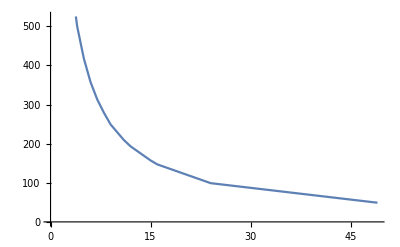

```mathematica
ListLinePlot@sizeOfSets
```

```mathematica
Apply[Plus,sizeOfSets]
```

8891